## Common elements

```mathematica
(* Load HEPMath package *)
Needs["HEPMath`"]
normKinVars={s-> sp+q2,s4-> sp+t1+u1,t-> t1+m2,u1p->u1-q2};
physAssump={m2>0,q2<0,s>0,sp>0,t1<0,u1<0,sp+t1+u1>0,s4>0,
s-s4-2m2>0,sp+t1>0,s+u1>0,(s-s4)^2-4m2 s>0,(sp+u1p)^2-4q2 t>0,
(* ?Marco *)(q2*s4-s*u1)>0,(q2*s4+4*m2*(q2-s-t1)-s*u1)>0(* ? *)
}/.normKinVars;

physParameterPoints={
{q2->-5,u1->-25,t1->-15,sp->115,m2->0.5},
{q2->-5,u1->-25,t1->-15,sp->115,m2->1.0},
{q2->-6,u1->-25,t1->-15,sp->115,m2->0.5},
{q2->-5,u1->-25,t1->-15,sp->120,m2->0.5}
};
Do[Module[{l,v},l=physAssump/.p;v=And@@l;If[Not[v],Print[p, " doesn't match assumptions: ",l]]],{p,physParameterPoints}]

(* total cross section parameters *)
ηOfs[s_]=s/(4m2)-1;
sOfη[η_]=(1+η)*(4m2);
ρOfs[s_]=4m2/s;
sOfρ[ρ_]=4m2/ρ;
βOfρ[ρ_]=Sqrt[1-ρ];
ρOfβ[β_]=1-β^2;
χOfβ[β_]=(1-β)/(1+β);
normTotalCSVars={ρ-> ρOfs[s],β-> βOfρ@ρOfs[s],η-> ηOfs[s],χ->χOfβ@βOfρ@ρOfs[s]};

(* color factors *)
normColor={Kgγ-> 1/(NC^2-1),Kqγ-> 1/NC,CA->1/NC,CF-> (NC^2-1)/(2NC),NC-> 3};
normColor=(First@#-> (Last@#/.normColor))&/@normColor;

(* tools *)
getLinearCoefficientList[e_,logs_]:=Module[{ar,pos0,pos1,allPos},
ar=CoefficientList[e,logs];
pos0=Table[1,{Length@logs}];
pos1=pos0;
pos1[[1]]=2;
allPos=Join[{pos0},Table[RotateRight[pos1,n-1],{n,Length@logs}]];
Table[Part@@Flatten[{{ar},p},1],{p,allPos}]
];
getAllSymbols=e↦ DeleteDuplicates[Reap[Map[If[Head[#]==Symbol,Sow[#]]&,e,Infinity]][[2]][[1]]];
```

## Matrix elements

```mathematica
<<"~/Physik/PhD/MMa/data/ElProduction.Me.m";
```

Take::take: Cannot take positions 1 through 1 in {}.

General::stop: Further output of Take :: take will be suppressed during this calculation.

## Born γ*+g → Q+Qbar

### Total cross sections

```mathematica
Module[{f,int},
f[t1_]=Integrate[Limit[BGQED/.{Dim->4+ϵ,u1-> -t1 - sp},ϵ-> 0],t1];
int=FullSimplify[f[sp/2(β-1)] - f[sp/2(-β-1)]];
σGg=2π*int/sp^2
]
Module[{f,int},
f[t1_]=Integrate[BLQED/.{u1-> -t1 - sp},t1];
int=FullSimplify[f[sp/2(β-1)] - f[sp/2(-β-1)]];
σLg=2π*2*int/sp^2
]
σTg=σGg+1/2σLg;
Module[{f,int},
f[t1_]=Integrate[Limit[BPQED/.{Dim->4+ϵ,u1-> -t1 - sp},ϵ-> 0],t1];
int=FullSimplify[f[sp/2(β-1)] - f[sp/2(-β-1)]];
σPg=2π*int/sp^2
]
```

(2 π ((2 β (8 m2 (2 m2+q2)-sp^2 (-1+β^2)))/(-1+β^2)+(8 m2^2-2 q2^2-4 m2 sp-sp (2 q2+sp)) (Log[sp (-1+β)]-Log[-sp (1+β)]-Log[sp (1+β)]+Log[sp-sp β])))/sp^3

-(16 π q2 ((q2+sp) β+m2 (Log[sp (-1+β)]-Log[-sp (1+β)]-Log[sp (1+β)]+Log[sp-sp β])))/sp^3

(2 π (2 β (-8 m2+(2 q2+sp) (-1+β^2))+(2 q2+sp) (-1+β^2) (Log[sp (-1+β)]-Log[-sp (1+β)]-Log[sp (1+β)]+Log[sp-sp β])))/(sp^2 (-1+β^2))

#### Check to Nucl.Phys.B 392-162

```mathematica
σLgref=16π(-q2 s)/sp^3 (β + 2m2/s Log[χ]);
σTref=4π/sp^3(-((s+q2)^2 + 4m2 s)β-(s^2+q2^2 + 4m2 s -8m2^2)Log[χ]);
FullSimplify[(σLgref-σLg)/.normTotalCSVars/.normKinVars,Assumptions-> {m2>0,0≤ 4m2/(sp+q2)≤ 1}]
FullSimplify[(σTref-σTg)/.normTotalCSVars/.normKinVars,Assumptions-> {m2>0,0≤ 4m2/(sp+q2)≤ 1}]
```

0

0

#### plots

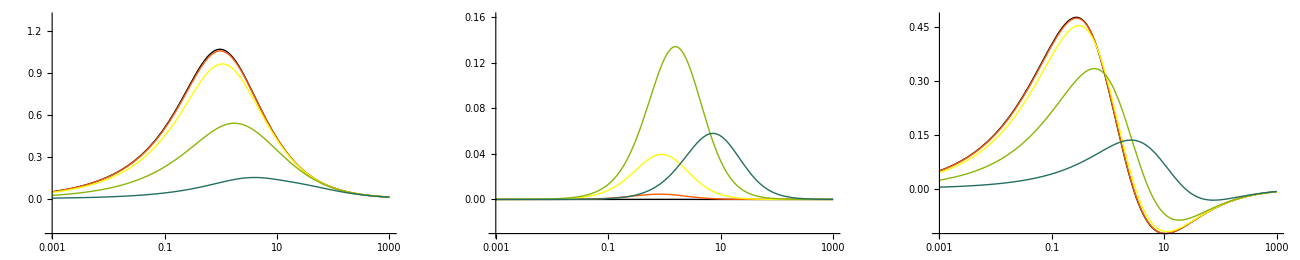

```mathematica
Module[{c0g},
c0g[var_][sV_,Q2V_,m2V_]:=Module[{sig,psNorm},
sig[T]=σTg;
sig[L]=σLg;
sig[P]=σPg;
psNorm[T]=psNorm[L]=psNorm[P]=Kgγ*NC*CF/.normColor;
(psNorm[var]*m2*(sig[var]/.normTotalCSVars/.normKinVars))//.{sp-> sV+Q2V,q2->-Q2V,m2-> m2V}
];
Show[GraphicsRow[{
LogLinearPlot[Evaluate@Table[c0g[T][sOfη@η,Q2,4.75^2],{Q2,{1*^-2,1,10,10^2,10^3}}],{η,1*^-3,1*^3},PlotRange-> {Full,{-.25,1.3}},PlotStyle->ColorData[3,"ColorList"]],
LogLinearPlot[Evaluate@Table[c0g[L][sOfη@η,Q2,4.75^2],{Q2,{1*^-2,1,10,10^2,10^3}}],{η,1*^-3,1*^3},PlotRange-> {Full,{-.03,.16}},PlotStyle->ColorData[3,"ColorList"]],
LogLinearPlot[Evaluate@Table[c0g[P][sOfη@η,Q2,4.75^2],{Q2,{1*^-2,1,10,10^2,10^3}}],{η,1*^-3,1*^3},PlotRange-> Full,PlotStyle->ColorData[3,"ColorList"]]
}],ImageSize-> 1300]
]
```

## Common NLO

```mathematica
<<"~/Physik/PhD/MMa/data/ElProduction.PsInt.m";
```

## NLO γ*+q → Q+Qbar+q

### ∫ A1 dΩ_n

#### Compute

```mathematica
(* build integrals *)
getPsIA1[coeff_] := MapIndexed[{e,path}↦If[e===0,0,psI[1/Times@@({tp,u7}^({3,3}-path))]],coeff,{2}];
getPsIA1k2[coeff_] := MapIndexed[{e,path}↦If[e===0,0,psIk2[1/Times@@({tp,u7}^({3,3}-path))]],coeff,{2}];
psIAG1=getPsIA1[CoeffAG1];
psIAL1=getPsIA1[CoeffAL1];
psIAP1k0=getPsIA1[CoeffAP1k0];
psIAP1k2=getPsIA1k2[CoeffAP1k2];
psLogsA1={psLog2[S1][u7],psLog3[S1][u7]};
```

```mathematica
(* compute pole terms *)
IntAG1pole =Expand@Total[Coefficient[CoeffAG1,ϵ,0]*Coefficient[psIAG1,ϵ,-1],2];
IntAL1pole =Expand@Total[Coefficient[CoeffAL1,ϵ,0]*Coefficient[psIAL1,ϵ,-1],2];
IntAP1pole =Expand@Total[Coefficient[CoeffAP1k0,ϵ,0]*Coefficient[psIAP1k0,ϵ,-1],2];
(* compute finite terms *)
IntAG1finite =Expand@Total[Coefficient[CoeffAG1,ϵ,0]*Coefficient[psIAG1,ϵ,0],2]+Expand@Total[Coefficient[CoeffAG1,ϵ,1]*Coefficient[psIAG1,ϵ,-1],2];
IntAL1finite =Expand@Total[Coefficient[CoeffAL1,ϵ,0]*Coefficient[psIAL1,ϵ,0],2]+Expand@Total[Coefficient[CoeffAL1,ϵ,1]*Coefficient[psIAL1,ϵ,-1],2];
IntAP1finite =Expand@Total[Coefficient[CoeffAP1k0,ϵ,0]*Coefficient[psIAP1k0,ϵ,0],2]+Expand@Total[Coefficient[CoeffAP1k0,ϵ,1]*Coefficient[psIAP1k0,ϵ,-1],2]+Expand@Total[Coefficient[CoeffAP1k2,ϵ,0]*Coefficient[psIAP1k2,ϵ,0],2];
```

#### check to Nucl.Phys.B 392-162

```mathematica
IntAG1poleref=((sp+t1)/u1^2 )*((s4^2+(sp+t1)^2)/(sp+t1)^2)*(
-(t1^2+(sp+t1)^2)/(t1(sp+t1))
+4m2 sp/(t1 u1)(1-m2 sp/(t1 u1)) + 2sp q2/(t1 u1)-2q2^2(sp+t1)/(t1 u1^2)
-2m2 q2/(t1^2 u1^2)(t1^2 + (sp+t1)^2)
);
IntAL1poleref = (sp+t1)^3/u1^4(s4^2+(sp+t1)^2)/(sp+t1)^2 4q2/sp^2*(sp t1 (u1-q2) - m2 sp^2 - q2 t1^2)/t1/(sp+t1);

FullSimplify[((IntAG1pole)/IntAG1poleref)/.normKinVars]
FullSimplify[((IntAG1pole*s4/(4π(s4+m2)))- IntAG1poleref)/.normKinVars]
FullSimplify[((IntAL1pole)/IntAL1poleref)/.normKinVars]
FullSimplify[(IntAL1pole*s4/(4π(s4+m2))-IntAL1poleref)/.normKinVars]
```

(4 π (m2+sp+t1+u1))/(sp+t1+u1)

0

(4 π (m2+sp+t1+u1))/(sp+t1+u1)

0

```mathematica
Module[{IntAG1poleRestref,diff},
IntAG1poleRestref=-((sp+t1)/u1^2 )*((s4^2+(sp+t1)^2)/(sp+t1)^2)*(
-2+4m2 sp/(t1 u1)(1-m2 sp/(t1 u1))-4m2 q2/(t1 u1^2)(sp+t1)
)
-(t1^2+(sp+t1)^2)/(t1(sp+t1)^2);
diff=(s4/((s4+m2)4π))*Total[Coefficient[Take[CoeffAG1,2],ϵ,1]*Coefficient[Take[psIAG1,2],ϵ,-1],2];
(*Print@Simplify@Expand[diff/.normKinVars];
Print@Simplify@Expand[(IntAG1poleRestref)/.normKinVars];
Print@Simplify@Expand[(IntAG1poleref)/.normKinVars];*)
Print@Simplify@Expand[((IntAG1poleref+IntAG1poleRestref)-2diff)/.normKinVars];
]
```

0

#### Check to Marco

```mathematica
Marco`IntAG1= << "~/Physik/PhD/Marco/recalc/data/IntAG1";
Marco`IntAL1= << "~/Physik/PhD/Marco/recalc/data/IntAL1";
```

```mathematica
(* pole *)
Simplify[((Coefficient[Marco`IntAG1,eps,-1]/8)-(IntAG1pole))/.normKinVars]
Simplify[((Coefficient[Marco`IntAL1,eps,-1]/8)-(IntAL1pole))/.normKinVars]
```

0

0

```mathematica
(* detect logs for replacement *)
DeleteDuplicates[Reap[Coefficient[Marco`IntAG1,eps,0]/.{Log[x_]:> Log[Sow[x]]}][[2]][[1]]]
DeleteDuplicates[Reap[Coefficient[Marco`IntAL1,eps,0]/.{Log[x_]:> Log[Sow[x]]}][[2]][[1]]]
```

{((m2+s4) t1^2 u1^2)/((-q2+s+t1)^2 (q2 s4 t1+m2 (-q2+s+u1)^2)),(2 m2 (q2-s-u1)+s4 (2 q2-s-u1+√(-4 m2 q2+s^2-4 q2 s4+2 s u1+u1^2)))/(2 m2 (q2-s-u1)-s4 (-2 q2+s+u1+√(-4 m2 q2+s^2-4 q2 s4+2 s u1+u1^2)))}

{((m2+s4) t1^2 u1^2)/((-q2+s+t1)^2 (q2 s4 t1+m2 (-q2+s+u1)^2)),(2 m2 (q2-s-u1)+s4 (2 q2-s-u1+√(-4 m2 q2+s^2-4 q2 s4+2 s u1+u1^2)))/(2 m2 (q2-s-u1)-s4 (-2 q2+s+u1+√(-4 m2 q2+s^2-4 q2 s4+2 s u1+u1^2))),(2 m2 (q2-s-u1)+s4 (2 q2-s-u1+√(-4 q2 (m2+s4)+(s+u1)^2)))/(2 m2 (q2-s-u1)-s4 (-2 q2+s+u1+√(-4 q2 (m2+s4)+(s+u1)^2)))}

```mathematica
(* finite terms *)
Module[{me,marco,diff},
Marco`IntAG1finite=(Coefficient[Marco`IntAG1,eps,0]/8/.{Log[x_]:> getPsLog[x]}/.normKinVars);
me=CoefficientList[IntAG1finite/.normKinVars,psLogsA1];
marco=CoefficientList[Marco`IntAG1finite,psLogsA1];
diff=Simplify[(me-marco)]
]
Module[{me,marco,diff},
Marco`IntAL1finite=(Coefficient[Marco`IntAL1,eps,0]/8/.{Log[x_]:> getPsLog[x]}/.normKinVars);
me=CoefficientList[IntAL1finite,psLogsA1]/.normKinVars;
marco=CoefficientList[Marco`IntAL1finite,psLogsA1];
diff=Simplify[(me-marco)]
]
```

{{0,0},{0,0}}

{{0,0},{0,0}}

### ∫ A2 dΩ_n

#### Compute

```mathematica
(* build integrals *)
getPsIA2[coeff_] := MapIndexed[{e,path}↦If[e===0,0,psI[1/Times@@({s5,up}^({3,3}-path))]],coeff,{2}];
psIAG2=getPsIA2[CoeffAG2];
psIAL2=getPsIA2[CoeffAL2];
psIAP2=getPsIA2[CoeffAP2];
psLogsA2={psLog3[S1][up],psLog3[S1][s5],psLog4[S1][tpsp,up],psLog4[S1][tpsp,s5]};
```

```mathematica
(* compute finite terms *)
IntAG2finite =Expand[Total[Coefficient[CoeffAG2,ϵ,0]*Coefficient[psIAG2,ϵ,0],2]/.normKinVars];
IntAL2finite =Expand[Total[Coefficient[CoeffAL2,ϵ,0]*Coefficient[psIAL2,ϵ,0],2]/.normKinVars];
IntAP2finite =Expand[Total[Coefficient[CoeffAP2,ϵ,0]*Coefficient[psIAP2,ϵ,0],2]/.normKinVars];

IntAG2finiteCoeffs=getLinearCoefficientList[IntAG2finite,psLogsA2];
IntAL2finiteCoeffs=getLinearCoefficientList[IntAL2finite,psLogsA2];
IntAP2finiteCoeffs=getLinearCoefficientList[IntAP2finite,psLogsA2];
```

#### Check to Marco

```mathematica
Marco`IntAG2= << "~/Physik/PhD/Marco/recalc/data/IntAG2";
Marco`IntAL2= << "~/Physik/PhD/Marco/recalc/data/IntAL2";
```

```mathematica
(* detect logs for replacement *)
DeleteDuplicates[Reap[Marco`IntAG2/.{Log[x_]:> Log[Sow[x]]}][[2]][[1]]]
DeleteDuplicates[Reap[Marco`IntAL2/.{Log[x_]:> Log[Sow[x]]}][[2]][[1]]]
```

{(2 m2 s+(s+√(-4 m2 s+(s-s4)^2)-s4) s4)/(2 m2 s-s4 (-s+√(-4 m2 s+(s-s4)^2)+s4)),(m2 (q2-s))/(m2 (q2-s)+s4 t1),((q2-s) (m2 q2+s4 t1))/(q2 (m2 (q2-s)+s4 t1)),(2 m2 q2+s4 (2 q2-s-u1+√(-4 q2 (m2+s4)+(s+u1)^2)))/(2 m2 q2-s4 (-2 q2+s+u1+√(-4 q2 (m2+s4)+(s+u1)^2)))}

{(2 m2 s+(s+√(-4 m2 s+(s-s4)^2)-s4) s4)/(2 m2 s-s4 (-s+√(-4 m2 s+(s-s4)^2)+s4)),(m2 (q2-s))/(m2 (q2-s)+s4 t1),((q2-s) (m2 q2+s4 t1))/(q2 (m2 (q2-s)+s4 t1)),(2 m2 q2+s4 (2 q2-s-u1+√(-4 q2 (m2+s4)+(s+u1)^2)))/(2 m2 q2-s4 (-2 q2+s+u1+√(-4 q2 (m2+s4)+(s+u1)^2)))}

```mathematica
(* finite terms *)
Module[{me,marco,logs,diff},
logs=psLogsA2;
Marco`IntAG2finite=(Marco`IntAG2/8/.{Log[x_]:> getPsLog[x]}/.normKinVars);
me=IntAG2finiteCoeffs;
marco=getLinearCoefficientList[Marco`IntAG2finite,logs];
diff=Simplify[(me-marco)];
Print@diff;

Marco`IntAL2finite=(Marco`IntAL2/8/.{Log[x_]:> getPsLog[x]}/.normKinVars);
me=IntAL2finiteCoeffs;
marco=getLinearCoefficientList[Marco`IntAL2finite,logs];
diff=Simplify[(me-marco)];
Print@diff;
]
```

{0,0,0,0,0}

{0,0,0,0,0}

### ∫ A3 dΩ_n

```mathematica
(* build integrals *)
getPsIA3[coeff_] := MapIndexed[{e,path}↦If[e===0,0,psI[1/Times@@({tp,u7,s5,up}^({2,2,2,2}-path))]],coeff,{4}];
psIAG3=getPsIA3[CoeffAG3];
psIAL3=getPsIA3[CoeffAL3];
psIAP3=getPsIA3[CoeffAP3];
psLogsA3={psLog2[S1][u7],psLog2[S1][s5],psLog2[S1][up],psLog3[S1][u7],psLog3[S1][s5],psLog3[S1][up],psLog4[S1][tpsp,s5],psLog4[S1][tpsp,up],psLog4[S2][u7,s5]};
```

```mathematica
(* check poles vanish *)
Module[{f,g0,g1,h},
h[ar_,pos_]:=Part@@Flatten[{{ar},{2,2,2,2}-pos},1];
f[l_]:=Select[l,First@#≥1&];
g0[l_,coeffs_,ints_]:=Sum[Coefficient[h[coeffs,e],ϵ,0]*Coefficient[h[ints,e],ϵ,-1],{e,f@l}];
g1[l_,coeffs_,ints_]:=Sum[Coefficient[h[coeffs,e],ϵ,1]*Coefficient[h[ints,e],ϵ,-1],{e,f@l}];
Print[(gj↦Simplify[gj@@{AG3List,CoeffAG3,psIAG3}/.normKinVars])/@{g0,g1}];
Print[(gj↦Simplify[gj@@{AL3List,CoeffAL3,psIAL3}/.normKinVars])/@{g0,g1}];
Print[(gj↦Simplify[gj@@{AP3List,CoeffAP3,psIAP3}/.normKinVars])/@{g0,g1}];
]
```

{0,0}

{0,0}

{0,0}

```mathematica
(* compute finite terms *)
IntAG3finite =Expand@Total[Coefficient[CoeffAG3,ϵ,0]*Coefficient[psIAG3,ϵ,0],4];
IntAL3finite =Expand@Total[Coefficient[CoeffAL3,ϵ,0]*Coefficient[psIAL3,ϵ,0],4];
IntAP3finite =Expand@Total[Coefficient[CoeffAP3,ϵ,0]*Coefficient[psIAP3,ϵ,0],4];
```

#### Check to Marco

```mathematica
Marco`IntAG3= (<< "~/Physik/PhD/Marco/recalc/data/IntAG3");
Marco`IntAL3= (<< "~/Physik/PhD/Marco/recalc/data/IntAL3");
```

```mathematica
(* detect logs for replacement *)
DeleteDuplicates[Reap[Marco`IntAG3/.{Log[x_]:> Log[Sow[x]]}][[2]][[1]]]
DeleteDuplicates[Reap[Marco`IntAL3/.{Log[x_]:> Log[Sow[x]]}][[2]][[1]]]
```

{(2 m2 s+(s+√(-4 m2 s+(s-s4)^2)-s4) s4)/(2 m2 s-s4 (-s+√(-4 m2 s+(s-s4)^2)+s4)),(m2 (q2-s))/(m2 (q2-s)+s4 t1),((q2-s) (m2 q2+s4 t1))/(q2 (m2 (q2-s)+s4 t1)),((m2+s4) (q2 s4-s u1)^2)/(m2 s^2 (-q2+s+t1)^2),((m2+s4) t1^2 u1^2)/((-q2+s+t1)^2 (q2 s4 t1+m2 (-q2+s+u1)^2)),((m2+s4) (2 q2^2+s s4-q2 (2 (s+t1)+u1))^2)/(q2 (-q2+s+t1)^2 (m2 q2+s4 t1)),(2 m2 q2+s4 (2 q2-s-u1+√(-4 q2 (m2+s4)+(s+u1)^2)))/(2 m2 q2-s4 (-2 q2+s+u1+√(-4 q2 (m2+s4)+(s+u1)^2))),(2 m2 (q2-s-u1)+s4 (2 q2-s-u1+√(-4 q2 (m2+s4)+(s+u1)^2)))/(2 m2 (q2-s-u1)-s4 (-2 q2+s+u1+√(-4 q2 (m2+s4)+(s+u1)^2))),(2 m2 s (-q2+s+u1)+s4 (-q2 s+2 q2 s4-s4 u1-√(4 m2 s (q2-u1) (-2 q2+s+u1)+(q2 s-2 q2 s4+s4 u1)^2)))/(2 m2 s (-q2+s+u1)+s4 (-q2 s+2 q2 s4-s4 u1+√(4 m2 s (q2-u1) (-2 q2+s+u1)+(q2 s-2 q2 s4+s4 u1)^2)))}

{(2 m2 s+(s+√(-4 m2 s+(s-s4)^2)-s4) s4)/(2 m2 s-s4 (-s+√(-4 m2 s+(s-s4)^2)+s4)),(m2 (q2-s))/(m2 (q2-s)+s4 t1),((q2-s) (m2 q2+s4 t1))/(q2 (m2 (q2-s)+s4 t1)),((m2+s4) (q2 s4-s u1)^2)/(m2 s^2 (-q2+s+t1)^2),((m2+s4) t1^2 u1^2)/((-q2+s+t1)^2 (q2 s4 t1+m2 (-q2+s+u1)^2)),((m2+s4) (2 q2^2+s s4-q2 (2 (s+t1)+u1))^2)/(q2 (-q2+s+t1)^2 (m2 q2+s4 t1)),(2 m2 q2+s4 (2 q2-s-u1+√(-4 q2 (m2+s4)+(s+u1)^2)))/(2 m2 q2-s4 (-2 q2+s+u1+√(-4 q2 (m2+s4)+(s+u1)^2))),(2 m2 (q2-s-u1)+s4 (2 q2-s-u1+√(-4 q2 (m2+s4)+(s+u1)^2)))/(2 m2 (q2-s-u1)-s4 (-2 q2+s+u1+√(-4 q2 (m2+s4)+(s+u1)^2))),(2 m2 s (-q2+s+u1)+s4 (-q2 s+2 q2 s4-s4 u1-√(4 m2 s (q2-u1) (-2 q2+s+u1)+(q2 s-2 q2 s4+s4 u1)^2)))/(2 m2 s (-q2+s+u1)+s4 (-q2 s+2 q2 s4-s4 u1+√(4 m2 s (q2-u1) (-2 q2+s+u1)+(q2 s-2 q2 s4+s4 u1)^2)))}

```mathematica
Simplify[Coefficient[Marco`IntAG3,eps,-1]/.normKinVars]
Simplify[Coefficient[Marco`IntAL3,eps,-1]/.normKinVars]
```

0

0

```mathematica
(* finite terms *)
Module[{logs,me,marco,diff},
(* all logs appear as single element -> linearize *)
logs=psLogsA3;

Marco`IntAG3finite=(Coefficient[Marco`IntAG3,eps,0]/16/.{Log[x_]:> getPsLog[x]}/.normKinVars);
me=getLinearCoefficientList[Expand@IntAG3finite/.normKinVars,logs];
marco=getLinearCoefficientList[Expand@Marco`IntAG3finite,logs];
diff=Simplify[(me-marco)];
Print@diff;

Marco`IntAL3finite=(Coefficient[Marco`IntAL3,eps,0]/16/.{Log[x_]:> getPsLog[x]}/.normKinVars);
me=getLinearCoefficientList[Expand@IntAL3finite/.normKinVars,logs];
marco=getLinearCoefficientList[Expand@Marco`IntAL3finite,logs];
diff=Simplify[(me-marco)];
Print@diff;
]
```

{0,0,0,0,0,0,0,0,0,0}

{0,0,0,0,0,0,0,0,0,0}

### Mass factorization

```mathematica
FullSimplify[IntAP1pole]
FullSimplify[((BPQED/.{sp-> x1 sp, t1->x1 t1})*(2-x1)*1/x1*1/(sp+t1))/.{x1-> -u1/(sp+t1)}]
```

(4 h π (m2+s4) (sp^2+2 sp t1+2 t1^2) (2 (sp+t1)+u1) (2 m2 sp^2+2 q2 t1 (sp+t1)-sp t1 u1))/(s4 sp t1^2 (sp+t1)^2 u1^2)

((sp^2+2 sp t1+2 t1^2) (2 (sp+t1)+u1) (2 m2 sp^2+2 q2 t1 (sp+t1)-sp t1 u1))/(sp t1^2 (sp+t1)^2 u1^2)

```mathematica
Module[{a,Sϵ,Pgq,
ps2to2AtNLOG,ps2to2AtNLOL,
split,BornFactor,ps2to3,x1,
shiftedBornG,shiftedBornL,shiftedBornP,massCounterG,massCounterL,massCounterP,n,
h0v,h0,h1v,h1
},
a[G]=1;
a[L]=2(1+ϵ/2);
a[P]=1;
Sϵ=(4π)^(-2-ϵ/2);

BornFactor[i_]=32 α αS eH^2 Kgγ NC CF 1/(1+ϵ/2)^2 π^3 Sϵ/Gamma[1+ϵ/2]*a[i]*(((t1 u1p-sp m2)sp-q2 t1^2)/(sp^2 μ2))^(ϵ/2)/.{Kgγ-> Kqγ/(2CF)};
ps2to3[i_]=64 Kqγ α αS^2 NC CF 1/(1+ϵ/2) π^3 Sϵ^2 μ2^(-ϵ/2) /Gamma[1+ϵ]*a[i]*(((t1 u1p-sp m2)sp-q2 t1^2)/(sp^2 μ2))^(ϵ/2) (s4/(s4+m2))(s4^2/(s4+m2))^(ϵ/2);
ps2to2AtNLOG=1/2 Kqγ α αS^2 NC CF 1/(4π)^(ϵ/2)1/Gamma[1+ϵ/2]*(((t1 u1p-sp m2)sp-q2 t1^2)/(sp^2 μ2))^(ϵ/2);
ps2to2AtNLOL=2ps2to2AtNLOG;
Print["ps2to3[G]: ",ps2to3[G]/.{ϵ-> 0}, " ps2to3[L]: ",ps2to3[L]/.{ϵ-> 0}];
Print[];
n=CF Kqγ α αS^2 NC;
(*Print["ps2to3[G]: ",Simplify@Series[ps2to3[G]*(2π(s4+m2)/s4)4/n,{ϵ,0,1}]];
Print["BornFactor[G]: ",Simplify@Series[CF αS/2*BornFactor[G]/(eH^2 π)4/n,{ϵ,0,1}]];
Print["ps2to2AtNLOG: ",Simplify@Series[ps2to2AtNLOG 4/n,{ϵ,0,1}]];
Print["ps2to3[G]/ps2to2AtNLOG: ",Simplify[FunctionExpand@Series[FullSimplify[ps2to3[G]/ps2to2AtNLOG],{ϵ,0,1}]*(4π(s4+m2))/(s4)]];
Print[];
Print["ps2to3[L]: ",Simplify@Series[ps2to3[L]*(2π(s4+m2)/s4)2/n,{ϵ,0,1}]];
Print["BornFactor[L]: ",Simplify@Series[CF αS/2*BornFactor[L]/(eH^2 π)2/n,{ϵ,0,1}]];
Print["ps2to2AtNLOL: ",Simplify@Series[ps2to2AtNLOL 2/n,{ϵ,0,1}]];
Print["ps2to3[L]/ps2to2AtNLOL: ",Simplify[FunctionExpand@Series[FullSimplify[ps2to3[L]/ps2to2AtNLOL],{ϵ,0,1}]*(4π(s4+m2))/(s4)]];
Print[];*)
(*
Print["ps2to3[G]/BornFactor[G]: ",Simplify[FunctionExpand@Series[FullSimplify[ps2to3[G]/BornFactor[G]],{ϵ,0,1}]]];
Print["ps2to3[L]/BornFactor[L]: ",Simplify[FunctionExpand@Series[FullSimplify[ps2to3[L]/BornFactor[L]],{ϵ,0,1}]]];*)


Pgq[G][x_]= CF (1+(1-x)^2)/x;
Pgq[L][x_]= CF (1+(1-x)^2)/x;
Pgq[P][x_]= CF (2-x);
split[m_][x_]=Pgq[m][x](2/ϵ+EulerGamma-Log[4π]+Log[μF2/μ2]);
x1=-u1/(sp+t1);
shiftedBornG=((BornFactor[G]*(BGQED/.{Dim-> 4+ϵ}))/.normKinVars)/.{sp-> x1 sp, t1-> x1 t1};
shiftedBornL=((BornFactor[L]*(BLQED/.{Dim-> 4+ϵ}))/.normKinVars)/.{sp-> x1 sp, t1-> x1 t1};
shiftedBornP=((BornFactor[P]*(BPQED/.{Dim-> 4+ϵ}))/.normKinVars)/.{sp-> x1 sp, t1-> x1 t1};
massCounterG=αS/(2π)*split[G][x1]*shiftedBornG * 1/x1*1/(sp+t1);
massCounterL=αS/(2π)*split[L][x1]*shiftedBornL * 1/x1*1/(sp+t1);
massCounterP=αS/(2π)*split[P][x1]*shiftedBornP * 1/x1*1/(sp+t1);
massCounterGpole=Simplify@SeriesCoefficient[massCounterG,{ϵ,0,-1}];
massCounterLpole=Simplify@SeriesCoefficient[massCounterL,{ϵ,0,-1}];
massCounterPpole=Simplify@SeriesCoefficient[massCounterP,{ϵ,0,-1}];

Print["check poles G: ", Simplify[massCounterGpole-Simplify[((ps2to3[G]/.{ϵ-> 0})*eH^2IntAG1pole/.normKinVars)]]];
Print["check poles L: ", Simplify[massCounterLpole-Simplify[((ps2to3[L]/.{ϵ-> 0})*eH^2IntAL1pole/.normKinVars)]]];
Print["check poles P: ", Simplify[massCounterPpole-Simplify[((ps2to3[P]/.{ϵ-> 0})*eH^2IntAP1pole/.{h-> 1}/.normKinVars)]]];
Print[];

h1v=(2 (2 m2+q2) (sp+t1) (m2 sp^2+q2 t1 (sp+t1))-2 (2 m2+q2) sp t1 (sp+t1) u1+t1 (sp^2+2 sp t1+2 t1^2) u1^2);
(*Print["massCounterG: ",FullSimplify[FullSimplify@Series[(massCounterG/.normKinVars),{ϵ,0,0}]/.{h1v-> h1,Simplify[q2/(2m2+q2)h1v]-> q2/(2m2+q2)h1}]];
Print["massCounterL: ",FullSimplify@Series[massCounterL/.normKinVars,{ϵ,0,0}]];
Print[];*)

massCounterGfinite=Simplify@SeriesCoefficient[massCounterG,{ϵ,0,0}];
massCounterLfinite=Simplify@SeriesCoefficient[massCounterL,{ϵ,0,0}];
h0v=(4 m2^2 sp^2 (sp+t1)+2 m2 (sp+t1) (q2 (sp^2+2 sp t1+2 t1^2)-2 sp t1 u1)+t1 (2 q2^2 (sp+t1)^2-2 q2 sp (sp+t1) u1+(sp^2+2 sp t1+2 t1^2) u1^2));
(*Print["massCounterGfinite: ",Collect[Simplify[massCounterGfinite]/.{h0v-> h0},h0,Simplify]];
Print["massCounterLfinite: ",massCounterLfinite];
Print[];*)

(* compute finite contributions from poles *)
finiteFromPolesG=FullSimplify@Limit[(ps2to3[G]*IntAG1pole*eH^2/ϵ-massCounterG)/.normKinVars,ϵ-> 0];
finiteFromPolesL=FullSimplify@Limit[(ps2to3[L]*IntAL1pole*eH^2/ϵ-massCounterL)/.normKinVars,ϵ-> 0];
finiteFromPolesP=FullSimplify@Limit[(ps2to3[P]*(IntAP1pole/.{h-> 1})*eH^2/ϵ-massCounterP)/.normKinVars,ϵ-> 0];
Print["finiteFromPolesG: ",finiteFromPolesG];
Print["finiteFromPolesL:",finiteFromPolesL];
Print["finiteFromPolesP:",finiteFromPolesP];
]
```

ps2to3[G]: (CF Kqγ NC s4 α αS^2)/(4 π (m2+s4)) ps2to3[L]: (CF Kqγ NC s4 α αS^2)/(2 π (m2+s4))

check poles G: 0

check poles L: 0

check poles P: 0

finiteFromPolesG: 1/(2 t1^2 (sp+t1)^2 u1^4)CF eH^2 Kqγ NC (2 (sp+t1)^2+2 (sp+t1) u1+u1^2) α αS^2 (-4 m2 (sp+t1) (m2 sp^2+q2 t1 (sp+t1))+4 m2 sp t1 (sp+t1) u1+sp^2 t1 u1^2-(2 (2 m2+q2) (sp+t1) (m2 sp^2+q2 t1 (sp+t1))-2 (2 m2+q2) sp t1 (sp+t1) u1+t1 (sp^2+2 sp t1+2 t1^2) u1^2) (Log[(sp+t1+u1)^2/(m2+sp+t1+u1)]-Log[μ2]-Log[μF2/μ2]))

finiteFromPolesL:-(4 CF eH^2 Kqγ NC q2 (m2 sp^2+q2 t1 (sp+t1)-sp t1 u1) (2 (sp+t1)^2+2 (sp+t1) u1+u1^2) α αS^2 (1+Log[(sp+t1+u1)^2/(m2+sp+t1+u1)]-Log[μ2]-Log[μF2/μ2]))/(sp^2 t1 u1^4)

finiteFromPolesP:(CF eH^2 Kqγ NC (sp^2+2 sp t1+2 t1^2) (2 (sp+t1)+u1) (2 m2 sp^2+2 q2 t1 (sp+t1)-sp t1 u1) α αS^2 (1+Log[(sp+t1+u1)^2/(m2+sp+t1+u1)]-Log[μ2]-Log[μF2/μ2]))/(2 sp t1^2 (sp+t1)^2 u1^2)

#### check to Nucl.Phys.B 392-162

```mathematica
Module[{normLogs,diffG},
normLogs={Log[u_*v_]:>Log[u]+Log[v],Log[1/u_]:> -Log[u],Log[u_^v_]:> v*Log[u]};
finiteFromPolesGref=1/2Kqγ α αS^2 eH^2NC CF(
(Log[s4^2/(m2(s4+m2))]+Log[m2/μF2])(
(sp+t1)/u1^2)((s4^2+(sp+t1)^2)/(sp+t1)^2)((-(t1^2+(sp+t1)^2))/(t1(sp+t1))+4m2 sp/(t1 u1)(1-m2 sp/(t1 u1))
+2sp q2/(t1 u1)-2q2^2(sp+t1)/(t1 u1^2)-2m2 q2/(t1^2 u1^2)(t1^2+(sp+t1)^2))
+(sp+t1)/(u1^2)((s4^2+(sp+t1)^2)/(sp+t1)^2)(4m2 sp/(t1 u1))(1-m2 sp/(t1 u1))+2(sp+t1)/(u1^2)((s4^2+(sp+t1)^2)/(sp+t1)^2)(sp q2/(t1 u1)-(m2 q2(t1^2+(sp+t1)^2)/(t1^2 u1^2))-q2^2(sp+t1)/(t1 u1^2))-(t1^2+(sp+t1)^2)/(t1(sp+t1)^2)
);
diffG=1/(4π)Kqγ α αS^2eH^2CF  NC (s4/(s4+m2))*Total[Coefficient[Take[CoeffAG1,2],ϵ,1]*Coefficient[Take[psIAG1,2],ϵ,-1],2];
finiteFromPolesLref=Kqγ α αS^2 eH^2NC CF(Log[s4^2/(m2(s4+m2))]+Log[m2/μF2]+1)*((sp+t1)^3/(u1^4))((s4^2+(sp+t1)^2)/(sp+t1)^2)(4q2/sp^2)((sp t1 u1 - m2 sp^2 -q2 t1 (sp+t1))/(t1 (sp+t1)));
Print[Simplify@Expand[(finiteFromPolesG+diffG-finiteFromPolesGref)/.{μ2->m2}//.normLogs/.normKinVars]];
Print[Simplify@Expand[(finiteFromPolesL-finiteFromPolesLref)/.{μ2->m2}//.normLogs/.normKinVars]];
]
```

0

0

#### check to Marco

```mathematica
Marco`massCounterGpole =<<"~/Physik/PhD/Marco/recalc/data/factPoleG";
Marco`massCounterLpole =<<"~/Physik/PhD/Marco/recalc/data/factPoleL";
```

```mathematica
Module[{r,me,marco,diff},
r={AEM-> α, ALPS-> αS, EH-> eH,mu^2-> μ2};
me=massCounterGpole;
marco=-Simplify@Coefficient[Marco`massCounterGpole,eps,-1]//.r;
diff=Simplify[((me/(Kqγ NC))-marco)/.normKinVars];
Print@diff;

me=massCounterLpole;
marco=-Simplify@Coefficient[Marco`massCounterLpole,eps,-1]//.r;
diff=Simplify[((me/(Kqγ NC))-marco)/.normKinVars];
Print@diff;
]
```

0

(CF eH^2 (((4 m^4 (q2+sp)^2 (q2+sp+t1)-4 m^2 (q2+sp) t1 (q2+sp+t1) u1+t1 ((q2+sp)^2+2 (q2+sp) t1+2 t1^2) u1^2) (2 (q2+sp)^2+2 t1^2+2 t1 u1+u1^2+2 (q2+sp) (2 t1+u1)))/(q2+sp+t1)^2-(8 q2 t1 (2 sp^2+2 t1^2+2 t1 u1+u1^2+2 sp (2 t1+u1)) (m2 sp^2+t1 (q2 (sp+t1)-sp u1)))/sp^2) α αS^2)/(t1^2 u1^4)

```mathematica
Marco`massCounterGfinite =<<"~/Physik/PhD/Marco/recalc/data/factFiniteG";
Marco`massCounterLfinite =<<"~/Physik/PhD/Marco/recalc/data/factFiniteL";
```

```mathematica
Module[{r,me,marco,diff},
r={AEM-> α, ALPS-> αS, EH-> eH,Log[muf^2/mu^2]-> Log[μF2/μ2],1/mu^2-> 1/μ2};
me=massCounterGfinite;
marco=-Marco`massCounterGfinite//.r;
diff=Simplify[((me/(Kqγ NC))-marco)/.normKinVars];
Print@diff;

me=massCounterLfinite;
marco=-Marco`massCounterLfinite//.r;
diff=Simplify[((me/(Kqγ NC))-marco)/.normKinVars];
Print@diff;
]
```

0

1/(2 t1^2 u1^4)CF eH^2 α αS^2 (1/(q2+sp+t1)^2(2 (q2+sp)^2+4 (q2+sp) t1+2 t1^2+2 (q2+sp) u1+2 t1 u1+u1^2) (-8 m^4 (q2+sp)^3+8 EulerGamma m^4 (q2+sp)^3-8 m^4 (q2+sp)^2 t1+8 EulerGamma m^4 (q2+sp)^2 t1+8 m^2 (q2+sp)^2 t1 u1-8 EulerGamma m^2 (q2+sp)^2 t1 u1+8 m^2 (q2+sp) t1^2 u1-8 EulerGamma m^2 (q2+sp) t1^2 u1+2 EulerGamma (q2+sp)^2 t1 u1^2-2 (q2+sp) t1^2 u1^2+4 EulerGamma (q2+sp) t1^2 u1^2-2 t1^3 u1^2+4 EulerGamma t1^3 u1^2-8 m^4 (q2+sp)^3 Log[2]-8 m^4 (q2+sp)^2 t1 Log[2]+8 m^2 (q2+sp)^2 t1 u1 Log[2]+8 m^2 (q2+sp) t1^2 u1 Log[2]-2 (q2+sp)^2 t1 u1^2 Log[2]-4 (q2+sp) t1^2 u1^2 Log[2]-4 t1^3 u1^2 Log[2]-4 m^4 (q2+sp)^3 Log[π]-4 m^4 (q2+sp)^2 t1 Log[π]+4 m^2 (q2+sp)^2 t1 u1 Log[π]+4 m^2 (q2+sp) t1^2 u1 Log[π]-(q2+sp)^2 t1 u1^2 Log[π]-2 (q2+sp) t1^2 u1^2 Log[π]-2 t1^3 u1^2 Log[π]-4 m^4 (q2+sp)^3 Log[4 π]-4 m^4 (q2+sp)^2 t1 Log[4 π]+4 m^2 (q2+sp)^2 t1 u1 Log[4 π]+4 m^2 (q2+sp) t1^2 u1 Log[4 π]-(q2+sp)^2 t1 u1^2 Log[4 π]-2 (q2+sp) t1^2 u1^2 Log[4 π]-2 t1^3 u1^2 Log[4 π]+4 m^4 (q2+sp)^3 Log[(mu^2 (-m^2 (q2+sp)+t1 u1))/(q2+sp)]+4 m^4 (q2+sp)^2 t1 Log[(mu^2 (-m^2 (q2+sp)+t1 u1))/(q2+sp)]-4 m^2 (q2+sp)^2 t1 u1 Log[(mu^2 (-m^2 (q2+sp)+t1 u1))/(q2+sp)]-4 m^2 (q2+sp) t1^2 u1 Log[(mu^2 (-m^2 (q2+sp)+t1 u1))/(q2+sp)]+(q2+sp)^2 t1 u1^2 Log[(mu^2 (-m^2 (q2+sp)+t1 u1))/(q2+sp)]+2 (q2+sp) t1^2 u1^2 Log[(mu^2 (-m^2 (q2+sp)+t1 u1))/(q2+sp)]+2 t1^3 u1^2 Log[(mu^2 (-m^2 (q2+sp)+t1 u1))/(q2+sp)]+4 m^4 (q2+sp)^3 Log[μF2/μ2]+4 m^4 (q2+sp)^2 t1 Log[μF2/μ2]-4 m^2 (q2+sp)^2 t1 u1 Log[μF2/μ2]-4 m^2 (q2+sp) t1^2 u1 Log[μF2/μ2]+(q2+sp)^2 t1 u1^2 Log[μF2/μ2]+2 (q2+sp) t1^2 u1^2 Log[μF2/μ2]+2 t1^3 u1^2 Log[μF2/μ2])-(8 q2 t1 (2 sp^2+2 t1^2+2 t1 u1+u1^2+2 sp (2 t1+u1)) (m2 sp^2+t1 (q2 (sp+t1)-sp u1)) (-1+2 EulerGamma+Log[-(m2 sp^2+t1 (q2 (sp+t1)-sp u1))/(sp^2 μ2)]+Log[μF2/(16 π^2 μ2)]))/sp^2)

### Total cross sections

(s (4 t1^2+sp^2 (-1+β^2)))/(4 sp t1^2)

(s (-1+β^2+√(1-β^2)))/(√(1-β^2))

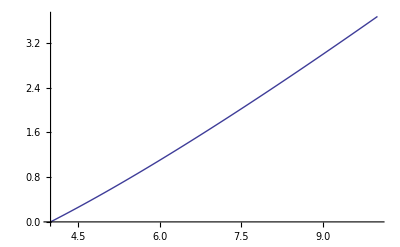

```mathematica
Module[{s4max,s4MaxVal},
s4max=(s/(sp t1)(t1+sp(1-β)/2)(t1+sp(1+β)/2));
Print@Simplify@Together@D[s4max,t1];
s4MaxVal=Simplify[s4max/.{t1-> -sp/2Sqrt[1-β^2]}];
Print@s4MaxVal;
Print@Plot[s4MaxVal/.normTotalCSVars/.{m2-> 1},{s,4,10}]
]
```

```mathematica
Module[{s4max,Mt1min,Mt1max,psNorm,ker,int,logs,s4MaxVal},
s4max=(s/(sp t1)(t1+sp(1-β)/2)(t1+sp(1+β)/2))/.normTotalCSVars/.normKinVars;
s4MaxVal=Simplify[s4max/.{t1-> -sp/2Sqrt[1-β^2]}]/.normTotalCSVars/.normKinVars;
Mt1min=sp(1-β)/2/.normTotalCSVars/.normKinVars;
Mt1max=sp(1+β)/2/.normTotalCSVars/.normKinVars;
psNorm[G]=psNorm[P]=(1/(4π) Kqγ NC CF (s4/(s4+m2)))/.normColor;
psNorm[L]=(1/(2π) Kqγ NC CF (s4/(s4+m2)))/.normColor;
logs=(((r↦(First@r-> Log[Last@r]))/@Join[psLogList[S1],psLogList[S2]]));
ker[psTimesSig_]:=(m2/(4π))(psTimesSig/sp^2)/.logs/.normKinVars/.{u1-> s4-sp-t1};
int[p_,psTimesSig_]:=NIntegrate[(ker[psTimesSig]//.p) Boole[s4<(s4max//.p)],{s4,0,s4MaxVal//.p},{t1,-Mt1max//.p,-Mt1min//.p},Method->"AdaptiveMonteCarlo"];

c1q[proj_][sV_,Q2V_,m2V_]:=Module[{p,sig,psTimesSigPole,s4MaxValV,n},
p={sp-> sV+Q2V,q2->-Q2V,m2-> m2V};
s4MaxValV=s4MaxVal//.p;
n=eH^2 α αS^2;
sig[G]=IntAG1finite;
sig[L]=IntAL1finite;
sig[P]=IntAP1finite/.{h-> 1};
psTimesSigPole[G]=(finiteFromPolesG/.{Log[μF2/μ2]-> 0,μ2-> m2}/.normColor)/(n);
psTimesSigPole[L]=(finiteFromPolesL/.{Log[μF2/μ2]-> 0,μ2-> m2}/.normColor)/(n);
psTimesSigPole[P]=(finiteFromPolesP/.{Log[μF2/μ2]-> 0,μ2-> m2,h-> 1}/.normColor)/(n);
int[p,psNorm[proj]*sig[proj]+psTimesSigPole[proj]]
];

cbar1q[proj_][sV_,Q2V_,m2V_]:=Module[{p,psTimesSig,s4MaxValV,n},
p={sp-> sV+Q2V,q2->-Q2V,m2-> m2V};
s4MaxValV=s4MaxVal//.p;
n=eH^2 α αS^2;
psTimesSig[G]=Coefficient[finiteFromPolesG/.normColor,Log[μF2/μ2]]/(n);
psTimesSig[L]=Coefficient[finiteFromPolesL/.normColor,Log[μF2/μ2]]/n;
psTimesSig[P]=Coefficient[finiteFromPolesP/.normColor/.{h-> 1},Log[μF2/μ2]]/n;
int[p,psTimesSig[proj]]
];

d1q[proj_][sV_,Q2V_,m2V_]:=Module[{p,sig,s4MaxValV},
p={sp-> sV+Q2V,q2->-Q2V,m2-> m2V};
s4MaxValV=s4MaxVal//.p;
sig[G]=IntAG2finite;
sig[L]=IntAL2finite;
sig[P]=IntAP2finite/.{h-> 1};
int[p,psNorm[proj]*sig[proj]]
];

cd1q[proj_][sV_,Q2V_,m2V_]:=Module[{p,sig,s4MaxValV},
p={sp-> sV+Q2V,q2->-Q2V,m2-> m2V};
s4MaxValV=s4MaxVal//.p;
sig[G]=IntAG3finite;
sig[L]=IntAL3finite;
sig[P]=IntAP3finite/.{h-> 1};
int[p,psNorm[proj]*sig[proj]]
];
]
```

#### plots

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.0679121, 0.0431927}. NIntegrate obtained -0.000300431 and 0.0000108606 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.000442778 and 9.38074×10^-6 for the integral and error estimates.

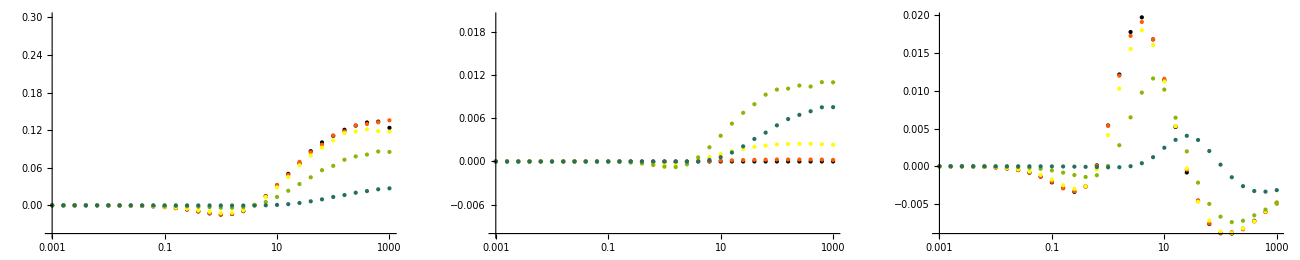

```mathematica
Module[{Qs,ηs,lLs,lGs,lTs,lPs},
Qs={1*^-2,1,10,100,1000};
ηs=Table[10^k,{k,-3,3,.2}];
lGs=Parallelize@Table[c1q[G][sOfη@η,Q,4.75^2],{Q,Qs},{η,ηs}];
(*Print@lGs;*)
lLs=Parallelize@Table[c1q[L][sOfη@η,Q,4.75^2],{Q,Qs},{η,ηs}];
(*Print@lLs;*)
lTs=lGs+1/2lLs;
lPs=Parallelize@Table[c1q[P][sOfη@η,Q,4.75^2],{Q,Qs},{η,ηs}];
(*Print@lPs;*)
Show[GraphicsRow[{
ListLogLinearPlot[Evaluate[(l↦Transpose[{ηs,Re@l}])/@lTs],PlotRange-> {Full,{-.045,.3}},PlotStyle->ColorData[3,"ColorList"]],
ListLogLinearPlot[Evaluate[(l↦Transpose[{ηs,Re@l}])/@lLs],PlotRange-> {Full,{-.01,.02}},PlotStyle->ColorData[3,"ColorList"]],
ListLogLinearPlot[Evaluate[(l↦Transpose[{ηs,Re@l}])/@lPs],PlotRange-> Full,PlotStyle->ColorData[3,"ColorList"]]
}],ImageSize-> 1300]
]
```

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 0.000020999 and 4.22629×10^-7 for the integral and error estimates.

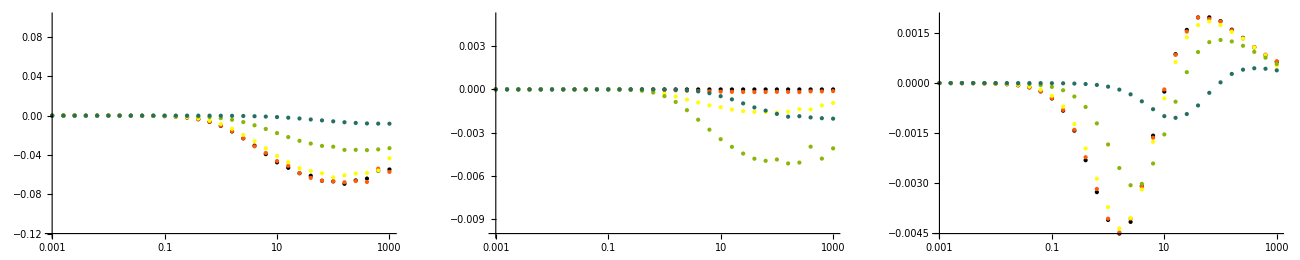

```mathematica
Module[{Qs,ηs,lLs,lGs,lTs,lPs},
Qs={1*^-2,1,10,100,1000};
ηs=Table[10^k,{k,-3,3,.2}];
lGs=Parallelize@Table[cbar1q[G][sOfη@η,Q,4.75^2],{Q,Qs},{η,ηs}];
(*Print@lGs;*)
lLs=Parallelize@Table[cbar1q[L][sOfη@η,Q,4.75^2],{Q,Qs},{η,ηs}];
(*Print@lLs;*)
lTs=lGs+1/2lLs;
lPs=Parallelize@Table[cbar1q[P][sOfη@η,Q,4.75^2],{Q,Qs},{η,ηs}];
(*Print@lPs;*)
Show[GraphicsRow[{
ListLogLinearPlot[Evaluate[(l↦Transpose[{ηs,Re@l}])/@lTs],PlotRange-> {Full,{-.12,.1}},PlotStyle->ColorData[3,"ColorList"]],
ListLogLinearPlot[Evaluate[(l↦Transpose[{ηs,Re@l}])/@lLs],PlotRange-> {Full,{-.01,.005}},PlotStyle->ColorData[3,"ColorList"]],
ListLogLinearPlot[Evaluate[(l↦Transpose[{ηs,Re@l}])/@lPs],PlotRange-> Full,PlotStyle->ColorData[3,"ColorList"]]
}],ImageSize-> 1300]
]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {4.01975×10^-6, 0.999943}. NIntegrate obtained -0.0000212968 and 6.01458×10^-7 for the integral and error estimates.

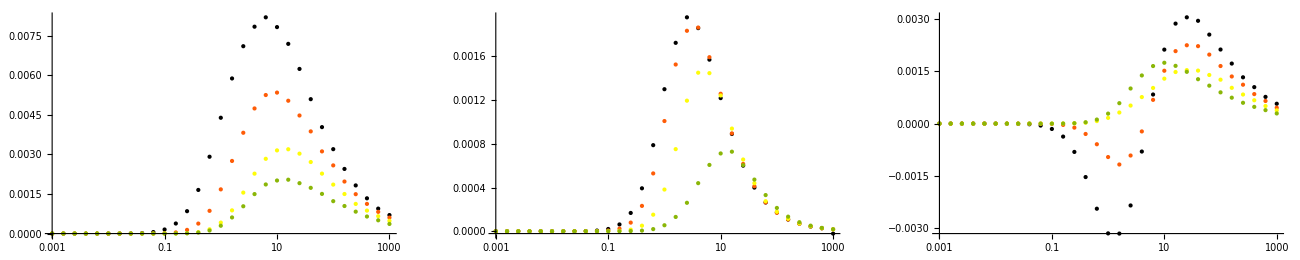

```mathematica
Module[{Qs,ηs,lLs,lGs,lTs,lPs},
Qs={1,10,100,1000};
ηs=Table[10^k,{k,-3,3,.2}];
lGs=Parallelize@Table[d1q[G][sOfη@η,Q,4.75^2],{Q,Qs},{η,ηs}];
(*Print@lGs;*)
lLs=Parallelize@Table[d1q[L][sOfη@η,Q,4.75^2],{Q,Qs},{η,ηs}];
(*Print@lLs;*)
lTs=lGs+1/2lLs;
lPs=Parallelize@Table[d1q[P][sOfη@η,Q,4.75^2],{Q,Qs},{η,ηs}];
(*Print@lPs;*)
Show[GraphicsRow[{
ListLogLinearPlot[Evaluate[(l↦Transpose[{ηs,Re@l}])/@lTs],PlotRange-> Full,PlotStyle->ColorData[3,"ColorList"]],
ListLogLinearPlot[Evaluate[(l↦Transpose[{ηs,Re@l}])/@lLs],PlotRange-> Full,PlotStyle->ColorData[3,"ColorList"]],
ListLogLinearPlot[Evaluate[(l↦Transpose[{ηs,Re@l}])/@lPs],PlotRange-> Full,PlotStyle->ColorData[3,"ColorList"]]
}],ImageSize-> 1300]
]
```

```mathematica
Module[{ηs,Qs,lL,lG,lT,lP},
ηs=Table[10^k,{k,-3,3,.2}];
lG=Parallelize@Table[cd1q[G][sOfη@η,1000,4.75^2],{η,ηs}];
Print@lG;
lL=Parallelize@Table[cd1q[L][sOfη@η,1000,4.75^2],{η,ηs}];
Print@lL;
lT=lG+1/2lL;
lP=Parallelize@Table[cd1q[P][sOfη@η,1000,4.75^2],{η,ηs}];
Print@lP;
]
```

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -2.90037×10^-16 and 2.19324×10^-17 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -6.18412×10^-15 and 5.09297×10^-16 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -2.26183×10^-13 and 8.44903×10^-14 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 2.28532×10^-11 and 1.17689×10^-12 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 1.67782×10^-13 and 6.75741×10^-15 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 1.78144×10^-10 and 1.56842×10^-11 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 1.45424×10^-14 and 1.49066×10^-15 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 4.75512×10^-16 and 1.06644×10^-16 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 6.60218×10^-12 and 3.37677×10^-13 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 3.22019×10^-10 and 4.18957×10^-12 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -2.78525×10^-13 and 2.26007×10^-14 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -1.0786×10^-7 and 1.13987×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -1.728×10^-9 and 5.66466×10^-11 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 1.72914×10^-8 and 3.49864×10^-9 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -1.19828×10^-11 and 1.62551×10^-10 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -5.18284×10^-7 and 6.94223×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -4.11941×10^-7 and 3.35881×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -8.80357×10^-7 and 1.88626×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -2.19107×10^-8 and 1.02551×10^-9 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -8.59074×10^-7 and 9.12151×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -4.33991×10^-8 and 6.4364×10^-9 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -5.11363×10^-7 and 4.88772×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -2.14726×10^-6 and 1.2708×10^-7 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 4.02529×10^-10 and 1.92791×10^-9 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -1.12753×10^-6 and 7.71135×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -6.93027×10^-7 and 9.67305×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -1.72166×10^-6 and 1.12185×10^-7 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -1.74023×10^-6 and 6.30699×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -2.5568×10^-9 and 4.5613×10^-10 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -1.63222×10^-7 and 1.35095×10^-7 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -1.71538×10^-6 and 1.01653×10^-7 for the integral and error estimates.

{-2.90037×10^-16,4.75512×10^-16,-6.18412×10^-15,1.45424×10^-14,1.67782×10^-13,-2.78525×10^-13,-2.26183×10^-13,6.60218×10^-12,2.28532×10^-11,3.22019×10^-10,1.78144×10^-10,-1.728×10^-9,-1.19828×10^-11,-2.5568×10^-9,-2.19107×10^-8,4.02529×10^-10,1.72914×10^-8,-4.33991×10^-8,-1.0786×10^-7,-8.80357×10^-7,-4.11941×10^-7,-5.11363×10^-7,-5.18284×10^-7,-8.59074×10^-7,-2.14726×10^-6,-6.93027×10^-7,-1.72166×10^-6,-1.71538×10^-6,-1.12753×10^-6,-1.63222×10^-7,-1.74023×10^-6}

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -1.01601×10^-12 and 2.9277×10^-13 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 1.19478×10^-16 and 6.62655×10^-18 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -5.77787×10^-16 and 2.49725×10^-16 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -3.79685×10^-13 and 9.93002×10^-15 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -6.70374×10^-19 and 1.8901×10^-19 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -3.68483×10^-20 and 4.914×10^-21 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 3.15619×10^-11 and 8.26412×10^-12 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -9.25951×10^-11 and 1.85315×10^-12 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 7.05364×10^-18 and 1.16814×10^-18 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -4.5036×10^-19 and 3.38611×10^-20 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -2.19436×10^-16 and 4.04138×10^-17 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -1.08373×10^-13 and 1.53665×10^-15 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -6.07468×10^-8 and 2.02809×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -4.20247×10^-7 and 7.64574×10^-9 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -1.1536×10^-6 and 2.24416×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -1.03077×10^-8 and 1.63753×10^-9 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -1.42727×10^-6 and 2.68068×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -7.1132×10^-7 and 1.54896×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -3.2375×10^-7 and 3.46099×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 2.75997×10^-11 and 4.96523×10^-11 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -2.07583×10^-9 and 2.04405×10^-10 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -3.05937×10^-7 and 1.78386×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -1.38107×10^-7 and 8.11118×10^-9 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -2.11392×10^-6 and 2.97505×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -4.13655×10^-7 and 4.5276×10^-9 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -4.04597×10^-8 and 5.55243×10^-10 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -5.04636×10^-8 and 2.14363×10^-9 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -8.83728×10^-8 and 4.86368×10^-9 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -7.49687×10^-8 and 2.80367×10^-9 for the integral and error estimates.

{-3.68483×10^-20,-4.5036×10^-19,-6.70374×10^-19,7.05364×10^-18,1.19478×10^-16,-2.19436×10^-16,-5.77787×10^-16,-1.08373×10^-13,-3.79685×10^-13,-8.65206×10^-12,-1.01601×10^-12,-9.25951×10^-11,3.15619×10^-11,2.75997×10^-11,-2.07583×10^-9,-4.04597×10^-8,-1.03077×10^-8,-8.83728×10^-8,-4.20247×10^-7,-7.1132×10^-7,-6.07468×10^-8,-1.42727×10^-6,-3.2375×10^-7,-2.11392×10^-6,-1.1536×10^-6,-3.05937×10^-7,-1.53342×10^-6,-1.38107×10^-7,-4.13655×10^-7,-7.49687×10^-8,-5.04636×10^-8}

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 2.01099×10^-14 and 3.31359×10^-16 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 4.73048×10^-12 and 7.56618×10^-14 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 1.33961×10^-15 and 2.15397×10^-17 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -1.48609×10^-14 and 5.44258×10^-15 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -3.45691×10^-11 and 1.68897×10^-11 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 1.88775×10^-11 and 1.12494×10^-12 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 1.15169×10^-13 and 1.49022×10^-15 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 7.26823×10^-13 and 3.2175×10^-13 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 2.53737×10^-16 and 1.06525×10^-16 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 2.01083×10^-13 and 1.97263×10^-14 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 2.66078×10^-11 and 4.25596×10^-12 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 2.05661×10^-9 and 5.42565×10^-11 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -1.27016×10^-8 and 3.69608×10^-9 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -3.29585×10^-11 and 9.69586×10^-10 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -7.46764×10^-7 and 2.26714×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -1.80567×10^-7 and 1.21188×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 2.80189×10^-8 and 1.89953×10^-9 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 1.49797×10^-9 and 1.73544×10^-10 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -5.03998×10^-7 and 3.35312×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -1.6676×10^-7 and 7.17436×10^-9 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -2.71354×10^-7 and 1.57345×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -1.03739×10^-7 and 1.71734×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -1.49804×10^-6 and 2.28248×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -1.81416×10^-7 and 7.02548×10^-9 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -5.61445×10^-8 and 3.50494×10^-9 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -7.6401×10^-7 and 3.67236×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 4.9915×10^-9 and 4.259×10^-10 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -8.50784×10^-7 and 3.50865×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -2.23536×10^-7 and 1.4514×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -9.20736×10^-7 and 2.82586×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -1.15516×10^-7 and 4.73921×10^-9 for the integral and error estimates.

{1.33961×10^-15,2.53737×10^-16,2.01099×10^-14,1.15169×10^-13,-1.48609×10^-14,2.01083×10^-13,4.73048×10^-12,7.26823×10^-13,1.88775×10^-11,2.66078×10^-11,-3.45691×10^-11,2.05661×10^-9,1.49797×10^-9,4.9915×10^-9,-3.29585×10^-11,2.80189×10^-8,-1.27016×10^-8,-1.6676×10^-7,-1.80567×10^-7,-1.03739×10^-7,-7.6401×10^-7,-9.20736×10^-7,-5.03998×10^-7,-8.50784×10^-7,-7.46764×10^-7,-1.49804×10^-6,-2.71354×10^-7,-2.23536×10^-7,-1.81416×10^-7,-1.15516×10^-7,-5.61445×10^-8}

#### analytic

```mathematica
Last@psLogsA2
Last@psLogsA2/.psLogList[S1]
FullSimplify@Last@IntAL2finiteCoeffs
```

psLog4[S1][tpsp,s5]

(m2 sp-t1 (sp+t1+u1))/(m2 sp)

(8 π q2 (m2+sp+t1+u1) (2 m2 q2 sp+t1 (-q2 t1+sp (sp+u1))))/(sp^2 (q2+sp)^2 t1 (sp+t1+u1))

```mathematica
Module[{list,log,i,s4max,coeff,k,j,Mt1min,Mt1max,r,vars,lVars},
list=psLogsA2/.psLogList[S1];
log=Log[Last@list/.{u1-> s4-sp-t1}];
coeff=FullSimplify[Last@IntAL2finiteCoeffs/.{u1-> s4-sp-t1}]*(s4/(s4+m2));
Print[coeff,"*",log];
s4max=s/(sp t1)(t1+sp(1-ρ)/2)(t1+sp(1+ρ)/2);
i=Simplify@Integrate[(coeff)log,s4];
(*Print@i;*)
k=Simplify[Simplify[Limit[i,s4-> s4max]/.{ρ-> Sqrt[1-4m2/s]}/.normKinVars]-Limit[i,s4-> 0]];
Mt1min=sp(1-ρ)/2/.normTotalCSVars/.normKinVars;
Mt1max=sp(1+ρ)/2/.normTotalCSVars/.normKinVars;
j=Simplify@Integrate[k,t1];
Print@j;
r=Simplify@Together[Simplify@Limit[j,t1-> -Mt1min]-Simplify@Limit[j,t1-> -Mt1max]];

vars=Reap[Expand@r/.{Log[x_]:> Log[Sow[x,Log]],PolyLog[2,x_]:> PolyLog[2,Sow[x,PolyLog]]}][[2]];
vars=DeleteDuplicates/@vars;
lVars=MapIndexed[{e,i}↦(Log[e]-> l[First@i]),First@vars];
Print@lVars;
Print@FullSimplify[r/.lVars/.{l[3]->ll+l[6],l[1]-> -ll+l[4],l[2]-> ll+l[5]}/.{l[5]-> l[57]+l[7]}]
]
```

(8 π q2 (2 m2 q2 sp+t1 (s4 sp-(q2+sp) t1)))/(sp^2 (q2+sp)^2 t1)*Log[(m2 sp-s4 t1)/(m2 sp)]

1/(9 sp^3 (q2+sp)^2 t1)2 π q2 (72 m2^2 q2 sp^3+27 m2^2 sp^4-216 m2 q2^2 sp t1^2-288 m2 q2 sp^2 t1^2-39 q2^2 sp^2 t1^2-72 m2 sp^3 t1^2-78 q2 sp^3 t1^2-39 sp^4 t1^2+6 q2^2 sp t1^3+12 q2 sp^2 t1^3+6 sp^3 t1^3+13 q2^2 t1^4+26 q2 sp t1^4+13 sp^2 t1^4-18 m2 sp^2 (2 q2^2+3 q2 sp+sp^2) t1 Log[t1]^2+72 m2 q2^2 sp^2 t1 Log[sp+t1]+108 m2 q2 sp^3 t1 Log[sp+t1]+12 q2^2 sp^3 t1 Log[sp+t1]+36 m2 sp^4 t1 Log[sp+t1]+24 q2 sp^4 t1 Log[sp+t1]+12 sp^5 t1 Log[sp+t1]-36 m2 sp^2 (2 q2^2+3 q2 sp+sp^2) t1 Log[t1] (1+Log[(sp+t1)/sp]-Log[-((q2+sp) t1 (sp+t1))/(m2 sp^2)])+72 m2 q2^2 sp t1^2 Log[-((q2+sp) t1 (sp+t1))/(m2 sp^2)]+108 m2 q2 sp^2 t1^2 Log[-((q2+sp) t1 (sp+t1))/(m2 sp^2)]+18 q2^2 sp^2 t1^2 Log[-((q2+sp) t1 (sp+t1))/(m2 sp^2)]+36 m2 sp^3 t1^2 Log[-((q2+sp) t1 (sp+t1))/(m2 sp^2)]+36 q2 sp^3 t1^2 Log[-((q2+sp) t1 (sp+t1))/(m2 sp^2)]+18 sp^4 t1^2 Log[-((q2+sp) t1 (sp+t1))/(m2 sp^2)]-6 q2^2 t1^4 Log[-((q2+sp) t1 (sp+t1))/(m2 sp^2)]-12 q2 sp t1^4 Log[-((q2+sp) t1 (sp+t1))/(m2 sp^2)]-6 sp^2 t1^4 Log[-((q2+sp) t1 (sp+t1))/(m2 sp^2)]-36 m2 sp^2 (2 q2^2+3 q2 sp+sp^2) t1 PolyLog[2,-t1/sp])

{Log[-(sp (4 m2+q2+sp))/(2 (q2+sp))]→l[1],Log[1/2-(2 m2)/(q2+sp)]→l[2],Log[sp (1/2-(2 m2)/(q2+sp))]→l[3],Log[sp (-1/2+(2 m2)/(q2+sp))]→l[4],Log[1/2+(2 m2)/(q2+sp)]→l[5],Log[sp (1/2+(2 m2)/(q2+sp))]→l[6],Log[(-16 m2^2+(q2+sp)^2)/(4 m2 (q2+sp))]→l[7]}

1/(9 sp (q2+sp)^3 (-4 m2+q2+sp) (4 m2+q2+sp))2 π q2 (-12 ll sp (q2+sp)^5-2304 m2^4 (q2+sp) (2 q2 (-3+l[7])+sp (-2+l[7]))+256 m2^5 sp (-13+6 l[7])+48 m2^2 (q2+sp)^3 (6 q2 (-3+l[7])+sp (-6+4 ll+3 l[7]))-3 m2 (q2+sp)^4 (6 ll^2 (2 q2+sp)+sp (47-18 l[7])+12 ll (2 q2+sp) (2+l[57]))+16 m2^3 (q2+sp)^2 (36 q2 (-2+ll (4+ll+2 l[57]))+sp (127-60 l[7]+18 ll (4+ll+2 l[57])))+36 m2 (4 m2-q2-sp) (q2+sp)^2 (4 m2+q2+sp) (2 q2+sp) (PolyLog[2,1/2-(2 m2)/(q2+sp)]-PolyLog[2,1/2+(2 m2)/(q2+sp)]))

```mathematica
Module[{list,log,i,s4max,coeff,k,j,Mt1min,Mt1max,r,vars,lVars},
list=psLogsA2/.psLogList[S1];
log=Log[list[[3]]/.{u1-> s4-sp-t1}];
coeff=FullSimplify[IntAL2finiteCoeffs[[1+3]]/.{u1-> s4-sp-t1}]*(s4/(s4+m2));
Print[coeff,"*",log];
s4max=s/(sp t1)(t1+sp(1-ρ)/2)(t1+sp(1+ρ)/2);
i=Simplify@Integrate[(coeff)log,s4];
(*Print@i;*)
k=Simplify[Simplify[Limit[i,s4-> s4max]/.{ρ-> Sqrt[1-4m2/s]}/.normKinVars]-Limit[i,s4-> 0]];
Mt1min=sp(1-ρ)/2/.normTotalCSVars/.normKinVars;
Mt1max=sp(1+ρ)/2/.normTotalCSVars/.normKinVars;
j=Simplify@Integrate[k,t1];
Print@j;
r=Simplify@Together[Simplify@Limit[j,t1-> -Mt1min]-Simplify@Limit[j,t1-> -Mt1max]];

vars=Reap[Expand@r/.{Log[x_]:> Log[Sow[x,Log]],PolyLog[2,x_]:> PolyLog[2,Sow[x,PolyLog]]}][[2]];
vars=DeleteDuplicates/@vars;
lVars=MapIndexed[{e,i}↦(Log[e]-> l[First@i]),First@vars];
Print@lVars;
Print@Simplify[r/.lVars]
]
```

-(8 π q2 (2 m2 q2 sp+t1 (s4 sp-(q2+sp) t1)))/(sp^2 (q2+sp)^2 t1)*Log[(q2 (m2 sp-s4 t1))/(sp (m2 q2+s4 t1))]

1/(3 sp^2 (q2+sp)^2)4 π q2 (-(3 m2^2 q2 sp^2)/t1-(3 m2^2 sp^3)/t1+13 m2 q2^2 t1+26 m2 q2 sp t1+13 m2 sp^2 t1-(64 m2^2 q2^2 √sp ArcTanh[(sp+2 t1)/(√sp √(-4 m2+sp))])/(√(-4 m2+sp))-(80 m2^2 q2 sp^(3/2) ArcTanh[(sp+2 t1)/(√sp √(-4 m2+sp))])/(√(-4 m2+sp))+(8 m2 q2^2 sp^(3/2) ArcTanh[(sp+2 t1)/(√sp √(-4 m2+sp))])/(√(-4 m2+sp))-(16 m2^2 sp^(5/2) ArcTanh[(sp+2 t1)/(√sp √(-4 m2+sp))])/(√(-4 m2+sp))+(4 m2 q2 sp^(5/2) ArcTanh[(sp+2 t1)/(√sp √(-4 m2+sp))])/(√(-4 m2+sp))+(2 q2^2 sp^(5/2) ArcTanh[(sp+2 t1)/(√sp √(-4 m2+sp))])/(√(-4 m2+sp))-(4 m2 sp^(7/2) ArcTanh[(sp+2 t1)/(√sp √(-4 m2+sp))])/(√(-4 m2+sp))+(4 q2 sp^(7/2) ArcTanh[(sp+2 t1)/(√sp √(-4 m2+sp))])/(√(-4 m2+sp))+(2 sp^(9/2) ArcTanh[(sp+2 t1)/(√sp √(-4 m2+sp))])/(√(-4 m2+sp))+(9 m2^2 q2^2 sp Log[m2 q2])/t1+6 m2 q2^2 t1 Log[m2 q2]+6 m2 q2 sp t1 Log[m2 q2]+(12 m2^2 q2 sp^2 Log[m2 sp])/t1+(3 m2^2 sp^3 Log[m2 sp])/t1+6 m2 q2 sp t1 Log[m2 sp]+6 m2 sp^2 t1 Log[m2 sp]+12 m2 q2^2 sp Log[t1]+18 m2 q2 sp^2 Log[t1]+6 m2 sp^3 Log[t1]+6 m2 q2^2 sp Log[t1]^2+9 m2 q2 sp^2 Log[t1]^2+3 m2 sp^3 Log[t1]^2-12 m2 q2^2 sp Log[sp+t1]-18 m2 q2 sp^2 Log[sp+t1]-2 q2^2 sp^2 Log[sp+t1]-6 m2 sp^3 Log[sp+t1]-4 q2 sp^3 Log[sp+t1]-2 sp^4 Log[sp+t1]+12 m2 q2^2 sp Log[t1] Log[(sp+t1)/sp]+18 m2 q2 sp^2 Log[t1] Log[(sp+t1)/sp]+6 m2 sp^3 Log[t1] Log[(sp+t1)/sp]-(12 m2^2 q2 sp^2 Log[-((q2+sp) t1 (sp+t1))/sp])/t1-(3 m2^2 sp^3 Log[-((q2+sp) t1 (sp+t1))/sp])/t1-6 m2 q2 sp t1 Log[-((q2+sp) t1 (sp+t1))/sp]-6 m2 sp^2 t1 Log[-((q2+sp) t1 (sp+t1))/sp]-12 m2 q2^2 sp Log[t1] Log[1+(2 t1)/(sp-√(sp (-4 m2+sp)))]-18 m2 q2 sp^2 Log[t1] Log[1+(2 t1)/(sp-√(sp (-4 m2+sp)))]-6 m2 sp^3 Log[t1] Log[1+(2 t1)/(sp-√(sp (-4 m2+sp)))]-12 m2 q2^2 sp Log[t1] Log[1+(2 t1)/(sp+√(sp (-4 m2+sp)))]-18 m2 q2 sp^2 Log[t1] Log[1+(2 t1)/(sp+√(sp (-4 m2+sp)))]-6 m2 sp^3 Log[t1] Log[1+(2 t1)/(sp+√(sp (-4 m2+sp)))]+(12 m2^2 q2 sp^2 Log[-(q2 t1 (sp+t1))/(sp (m2 sp+t1 (sp+t1)))])/t1+(3 m2^2 sp^3 Log[-(q2 t1 (sp+t1))/(sp (m2 sp+t1 (sp+t1)))])/t1-12 m2 q2^2 t1 Log[-(q2 t1 (sp+t1))/(sp (m2 sp+t1 (sp+t1)))]-12 m2 q2 sp t1 Log[-(q2 t1 (sp+t1))/(sp (m2 sp+t1 (sp+t1)))]-3 q2^2 sp t1 Log[-(q2 t1 (sp+t1))/(sp (m2 sp+t1 (sp+t1)))]-6 q2 sp^2 t1 Log[-(q2 t1 (sp+t1))/(sp (m2 sp+t1 (sp+t1)))]-3 sp^3 t1 Log[-(q2 t1 (sp+t1))/(sp (m2 sp+t1 (sp+t1)))]+2 q2 t1^3 Log[-(q2 t1 (sp+t1))/(sp (m2 sp+t1 (sp+t1)))]+(q2^2 t1^3 Log[-(q2 t1 (sp+t1))/(sp (m2 sp+t1 (sp+t1)))])/sp+sp t1^3 Log[-(q2 t1 (sp+t1))/(sp (m2 sp+t1 (sp+t1)))]-12 m2 q2^2 sp Log[t1] Log[-(q2 t1 (sp+t1))/(sp (m2 sp+t1 (sp+t1)))]-18 m2 q2 sp^2 Log[t1] Log[-(q2 t1 (sp+t1))/(sp (m2 sp+t1 (sp+t1)))]-6 m2 sp^3 Log[t1] Log[-(q2 t1 (sp+t1))/(sp (m2 sp+t1 (sp+t1)))]+q2^2 sp^2 Log[m2 sp+t1 (sp+t1)]+2 q2 sp^3 Log[m2 sp+t1 (sp+t1)]+sp^4 Log[m2 sp+t1 (sp+t1)]-(9 m2^2 q2^2 sp Log[((q2+sp) (m2 sp+t1 (sp+t1)))/sp])/t1-6 m2 q2^2 t1 Log[((q2+sp) (m2 sp+t1 (sp+t1)))/sp]-6 m2 q2 sp t1 Log[((q2+sp) (m2 sp+t1 (sp+t1)))/sp]+6 m2 sp (2 q2^2+3 q2 sp+sp^2) PolyLog[2,-t1/sp]-6 m2 sp (2 q2^2+3 q2 sp+sp^2) PolyLog[2,(2 t1)/(-sp+√(sp (-4 m2+sp)))]-12 m2 q2^2 sp PolyLog[2,-(2 t1)/(sp+√(sp (-4 m2+sp)))]-18 m2 q2 sp^2 PolyLog[2,-(2 t1)/(sp+√(sp (-4 m2+sp)))]-6 m2 sp^3 PolyLog[2,-(2 t1)/(sp+√(sp (-4 m2+sp)))])

{Log[m2 q2]→l[1],Log[m2 sp]→l[2],Log[-(sp (4 m2+q2+sp))/(2 (q2+sp))]→l[3],Log[(-4 m2+q2+sp)/(2 (q2+sp))]→l[4],Log[sp (1/2-(2 m2)/(q2+sp))]→l[5],Log[sp (-1/2+(2 m2)/(q2+sp))]→l[6],Log[(4 m2+q2+sp)/(2 (q2+sp))]→l[7],Log[sp (1/2+(2 m2)/(q2+sp))]→l[8],Log[(sp (-16 m2^2+(q2+sp)^2))/(4 (q2+sp))]→l[9],Log[(q2 (-4 m2+q2+sp) (4 m2+q2+sp))/(16 m2^2 sp+4 m2 (q2+sp)^2-sp (q2+sp)^2)]→l[10],Log[(16 m2^2 sp+4 m2 (q2+sp)^2-sp (q2+sp)^2)/(4 (q2+sp))]→l[11],Log[1+(sp (-4 m2+q2+sp))/((q2+sp) (-sp+√(sp (-4 m2+sp))))]→l[12],Log[1+(sp (4 m2+q2+sp))/((q2+sp) (-sp+√(sp (-4 m2+sp))))]→l[13],Log[1+((4 m2-q2-sp) sp)/((q2+sp) (sp+√(sp (-4 m2+sp))))]→l[14],Log[1-(sp (4 m2+q2+sp))/((q2+sp) (sp+√(sp (-4 m2+sp))))]→l[15]}

1/(3 sp^2 (q2+sp)^3 (-16 m2^2+(q2+sp)^2))4 π q2 (-832 m2^4 q2^2 sp+48 m2^3 q2^3 sp+52 m2^2 q2^4 sp-1664 m2^4 q2 sp^2+144 m2^3 q2^2 sp^2+208 m2^2 q2^3 sp^2-832 m2^4 sp^3+144 m2^3 q2 sp^3+312 m2^2 q2^2 sp^3+48 m2^3 sp^4+208 m2^2 q2 sp^4+52 m2^2 sp^5+(2048 m2^4 q2^3 √sp ArcTanh[(4 m2 √sp)/(√(-4 m2+sp) (q2+sp))])/(√(-4 m2+sp))-(128 m2^2 q2^5 √sp ArcTanh[(4 m2 √sp)/(√(-4 m2+sp) (q2+sp))])/(√(-4 m2+sp))+(4608 m2^4 q2^2 sp^(3/2) ArcTanh[(4 m2 √sp)/(√(-4 m2+sp) (q2+sp))])/(√(-4 m2+sp))-(256 m2^3 q2^3 sp^(3/2) ArcTanh[(4 m2 √sp)/(√(-4 m2+sp) (q2+sp))])/(√(-4 m2+sp))-(544 m2^2 q2^4 sp^(3/2) ArcTanh[(4 m2 √sp)/(√(-4 m2+sp) (q2+sp))])/(√(-4 m2+sp))+(16 m2 q2^5 sp^(3/2) ArcTanh[(4 m2 √sp)/(√(-4 m2+sp) (q2+sp))])/(√(-4 m2+sp))+(3072 m2^4 q2 sp^(5/2) ArcTanh[(4 m2 √sp)/(√(-4 m2+sp) (q2+sp))])/(√(-4 m2+sp))-(384 m2^3 q2^2 sp^(5/2) ArcTanh[(4 m2 √sp)/(√(-4 m2+sp) (q2+sp))])/(√(-4 m2+sp))-(960 m2^2 q2^3 sp^(5/2) ArcTanh[(4 m2 √sp)/(√(-4 m2+sp) (q2+sp))])/(√(-4 m2+sp))+(56 m2 q2^4 sp^(5/2) ArcTanh[(4 m2 √sp)/(√(-4 m2+sp) (q2+sp))])/(√(-4 m2+sp))+(4 q2^5 sp^(5/2) ArcTanh[(4 m2 √sp)/(√(-4 m2+sp) (q2+sp))])/(√(-4 m2+sp))+(512 m2^4 sp^(7/2) ArcTanh[(4 m2 √sp)/(√(-4 m2+sp) (q2+sp))])/(√(-4 m2+sp))-(896 m2^2 q2^2 sp^(7/2) ArcTanh[(4 m2 √sp)/(√(-4 m2+sp) (q2+sp))])/(√(-4 m2+sp))+(64 m2 q2^3 sp^(7/2) ArcTanh[(4 m2 √sp)/(√(-4 m2+sp) (q2+sp))])/(√(-4 m2+sp))+(20 q2^4 sp^(7/2) ArcTanh[(4 m2 √sp)/(√(-4 m2+sp) (q2+sp))])/(√(-4 m2+sp))+(128 m2^3 sp^(9/2) ArcTanh[(4 m2 √sp)/(√(-4 m2+sp) (q2+sp))])/(√(-4 m2+sp))-(448 m2^2 q2 sp^(9/2) ArcTanh[(4 m2 √sp)/(√(-4 m2+sp) (q2+sp))])/(√(-4 m2+sp))+(16 m2 q2^2 sp^(9/2) ArcTanh[(4 m2 √sp)/(√(-4 m2+sp) (q2+sp))])/(√(-4 m2+sp))+(40 q2^3 sp^(9/2) ArcTanh[(4 m2 √sp)/(√(-4 m2+sp) (q2+sp))])/(√(-4 m2+sp))-(96 m2^2 sp^(11/2) ArcTanh[(4 m2 √sp)/(√(-4 m2+sp) (q2+sp))])/(√(-4 m2+sp))-(16 m2 q2 sp^(11/2) ArcTanh[(4 m2 √sp)/(√(-4 m2+sp) (q2+sp))])/(√(-4 m2+sp))+(40 q2^2 sp^(11/2) ArcTanh[(4 m2 √sp)/(√(-4 m2+sp) (q2+sp))])/(√(-4 m2+sp))-(8 m2 sp^(13/2) ArcTanh[(4 m2 √sp)/(√(-4 m2+sp) (q2+sp))])/(√(-4 m2+sp))+(20 q2 sp^(13/2) ArcTanh[(4 m2 √sp)/(√(-4 m2+sp) (q2+sp))])/(√(-4 m2+sp))+(4 sp^(15/2) ArcTanh[(4 m2 √sp)/(√(-4 m2+sp) (q2+sp))])/(√(-4 m2+sp))-144 m2^3 q2^4 l[1]-384 m2^4 q2^2 sp l[1]-288 m2^3 q2^3 sp l[1]+24 m2^2 q2^4 sp l[1]-384 m2^4 q2 sp^2 l[1]-144 m2^3 q2^2 sp^2 l[1]+72 m2^2 q2^3 sp^2 l[1]+72 m2^2 q2^2 sp^3 l[1]+24 m2^2 q2 sp^4 l[1]-192 m2^3 q2^3 sp l[2]-384 m2^4 q2 sp^2 l[2]-432 m2^3 q2^2 sp^2 l[2]+24 m2^2 q2^3 sp^2 l[2]-384 m2^4 sp^3 l[2]-288 m2^3 q2 sp^3 l[2]+72 m2^2 q2^2 sp^3 l[2]-48 m2^3 sp^4 l[2]+72 m2^2 q2 sp^4 l[2]+24 m2^2 sp^5 l[2]+192 m2^3 q2^3 sp l[3]-12 m2 q2^5 sp l[3]+480 m2^3 q2^2 sp^2 l[3]-54 m2 q2^4 sp^2 l[3]+384 m2^3 q2 sp^3 l[3]-96 m2 q2^3 sp^3 l[3]+96 m2^3 sp^4 l[3]-84 m2 q2^2 sp^4 l[3]-36 m2 q2 sp^5 l[3]-6 m2 sp^6 l[3]+96 m2^3 q2^3 sp l[3]^2-6 m2 q2^5 sp l[3]^2+240 m2^3 q2^2 sp^2 l[3]^2-27 m2 q2^4 sp^2 l[3]^2+192 m2^3 q2 sp^3 l[3]^2-48 m2 q2^3 sp^3 l[3]^2+48 m2^3 sp^4 l[3]^2-42 m2 q2^2 sp^4 l[3]^2-18 m2 q2 sp^5 l[3]^2-3 m2 sp^6 l[3]^2+192 m2^3 q2^3 sp l[3] l[4]-12 m2 q2^5 sp l[3] l[4]+480 m2^3 q2^2 sp^2 l[3] l[4]-54 m2 q2^4 sp^2 l[3] l[4]+384 m2^3 q2 sp^3 l[3] l[4]-96 m2 q2^3 sp^3 l[3] l[4]+96 m2^3 sp^4 l[3] l[4]-84 m2 q2^2 sp^4 l[3] l[4]-36 m2 q2 sp^5 l[3] l[4]-6 m2 sp^6 l[3] l[4]-192 m2^3 q2^3 sp l[5]+12 m2 q2^5 sp l[5]-480 m2^3 q2^2 sp^2 l[5]-32 m2^2 q2^3 sp^2 l[5]+54 m2 q2^4 sp^2 l[5]+2 q2^5 sp^2 l[5]-384 m2^3 q2 sp^3 l[5]-96 m2^2 q2^2 sp^3 l[5]+96 m2 q2^3 sp^3 l[5]+10 q2^4 sp^3 l[5]-96 m2^3 sp^4 l[5]-96 m2^2 q2 sp^4 l[5]+84 m2 q2^2 sp^4 l[5]+20 q2^3 sp^4 l[5]-32 m2^2 sp^5 l[5]+36 m2 q2 sp^5 l[5]+20 q2^2 sp^5 l[5]+6 m2 sp^6 l[5]+10 q2 sp^6 l[5]+2 sp^7 l[5]-192 m2^3 q2^3 sp l[6]+12 m2 q2^5 sp l[6]-480 m2^3 q2^2 sp^2 l[6]+54 m2 q2^4 sp^2 l[6]-384 m2^3 q2 sp^3 l[6]+96 m2 q2^3 sp^3 l[6]-96 m2^3 sp^4 l[6]+84 m2 q2^2 sp^4 l[6]+36 m2 q2 sp^5 l[6]+6 m2 sp^6 l[6]-96 m2^3 q2^3 sp l[6]^2+6 m2 q2^5 sp l[6]^2-240 m2^3 q2^2 sp^2 l[6]^2+27 m2 q2^4 sp^2 l[6]^2-192 m2^3 q2 sp^3 l[6]^2+48 m2 q2^3 sp^3 l[6]^2-48 m2^3 sp^4 l[6]^2+42 m2 q2^2 sp^4 l[6]^2+18 m2 q2 sp^5 l[6]^2+3 m2 sp^6 l[6]^2-192 m2^3 q2^3 sp l[6] l[7]+12 m2 q2^5 sp l[6] l[7]-480 m2^3 q2^2 sp^2 l[6] l[7]+54 m2 q2^4 sp^2 l[6] l[7]-384 m2^3 q2 sp^3 l[6] l[7]+96 m2 q2^3 sp^3 l[6] l[7]-96 m2^3 sp^4 l[6] l[7]+84 m2 q2^2 sp^4 l[6] l[7]+36 m2 q2 sp^5 l[6] l[7]+6 m2 sp^6 l[6] l[7]+192 m2^3 q2^3 sp l[8]-12 m2 q2^5 sp l[8]+480 m2^3 q2^2 sp^2 l[8]+32 m2^2 q2^3 sp^2 l[8]-54 m2 q2^4 sp^2 l[8]-2 q2^5 sp^2 l[8]+384 m2^3 q2 sp^3 l[8]+96 m2^2 q2^2 sp^3 l[8]-96 m2 q2^3 sp^3 l[8]-10 q2^4 sp^3 l[8]+96 m2^3 sp^4 l[8]+96 m2^2 q2 sp^4 l[8]-84 m2 q2^2 sp^4 l[8]-20 q2^3 sp^4 l[8]+32 m2^2 sp^5 l[8]-36 m2 q2 sp^5 l[8]-20 q2^2 sp^5 l[8]-6 m2 sp^6 l[8]-10 q2 sp^6 l[8]-2 sp^7 l[8]+192 m2^3 q2^3 sp l[9]+384 m2^4 q2 sp^2 l[9]+432 m2^3 q2^2 sp^2 l[9]-24 m2^2 q2^3 sp^2 l[9]+384 m2^4 sp^3 l[9]+288 m2^3 q2 sp^3 l[9]-72 m2^2 q2^2 sp^3 l[9]+48 m2^3 sp^4 l[9]-72 m2^2 q2 sp^4 l[9]-24 m2^2 sp^5 l[9]+768 m2^4 q2^2 sp l[10]-192 m2^3 q2^3 sp l[10]-48 m2^2 q2^4 sp l[10]-256 m2^5 sp^2 l[10]+768 m2^4 q2 sp^2 l[10]-272 m2^3 q2^2 sp^2 l[10]-144 m2^2 q2^3 sp^2 l[10]-9 m2 q2^4 sp^2 l[10]+32 m2^3 q2 sp^3 l[10]-144 m2^2 q2^2 sp^3 l[10]-36 m2 q2^3 sp^3 l[10]+112 m2^3 sp^4 l[10]-48 m2^2 q2 sp^4 l[10]-54 m2 q2^2 sp^4 l[10]-36 m2 q2 sp^5 l[10]-9 m2 sp^6 l[10]-192 m2^3 q2^3 sp l[3] l[10]+12 m2 q2^5 sp l[3] l[10]-480 m2^3 q2^2 sp^2 l[3] l[10]+54 m2 q2^4 sp^2 l[3] l[10]-384 m2^3 q2 sp^3 l[3] l[10]+96 m2 q2^3 sp^3 l[3] l[10]-96 m2^3 sp^4 l[3] l[10]+84 m2 q2^2 sp^4 l[3] l[10]+36 m2 q2 sp^5 l[3] l[10]+6 m2 sp^6 l[3] l[10]+192 m2^3 q2^3 sp l[6] l[10]-12 m2 q2^5 sp l[6] l[10]+480 m2^3 q2^2 sp^2 l[6] l[10]-54 m2 q2^4 sp^2 l[6] l[10]+384 m2^3 q2 sp^3 l[6] l[10]-96 m2 q2^3 sp^3 l[6] l[10]+96 m2^3 sp^4 l[6] l[10]-84 m2 q2^2 sp^4 l[6] l[10]-36 m2 q2 sp^5 l[6] l[10]-6 m2 sp^6 l[6] l[10]+144 m2^3 q2^4 l[11]+384 m2^4 q2^2 sp l[11]+288 m2^3 q2^3 sp l[11]-24 m2^2 q2^4 sp l[11]+384 m2^4 q2 sp^2 l[11]+144 m2^3 q2^2 sp^2 l[11]-72 m2^2 q2^3 sp^2 l[11]-72 m2^2 q2^2 sp^3 l[11]-24 m2^2 q2 sp^4 l[11]+192 m2^3 q2^3 sp l[6] l[12]-12 m2 q2^5 sp l[6] l[12]+480 m2^3 q2^2 sp^2 l[6] l[12]-54 m2 q2^4 sp^2 l[6] l[12]+384 m2^3 q2 sp^3 l[6] l[12]-96 m2 q2^3 sp^3 l[6] l[12]+96 m2^3 sp^4 l[6] l[12]-84 m2 q2^2 sp^4 l[6] l[12]-36 m2 q2 sp^5 l[6] l[12]-6 m2 sp^6 l[6] l[12]-192 m2^3 q2^3 sp l[3] l[13]+12 m2 q2^5 sp l[3] l[13]-480 m2^3 q2^2 sp^2 l[3] l[13]+54 m2 q2^4 sp^2 l[3] l[13]-384 m2^3 q2 sp^3 l[3] l[13]+96 m2 q2^3 sp^3 l[3] l[13]-96 m2^3 sp^4 l[3] l[13]+84 m2 q2^2 sp^4 l[3] l[13]+36 m2 q2 sp^5 l[3] l[13]+6 m2 sp^6 l[3] l[13]+192 m2^3 q2^3 sp l[6] l[14]-12 m2 q2^5 sp l[6] l[14]+480 m2^3 q2^2 sp^2 l[6] l[14]-54 m2 q2^4 sp^2 l[6] l[14]+384 m2^3 q2 sp^3 l[6] l[14]-96 m2 q2^3 sp^3 l[6] l[14]+96 m2^3 sp^4 l[6] l[14]-84 m2 q2^2 sp^4 l[6] l[14]-36 m2 q2 sp^5 l[6] l[14]-6 m2 sp^6 l[6] l[14]-192 m2^3 q2^3 sp l[3] l[15]+12 m2 q2^5 sp l[3] l[15]-480 m2^3 q2^2 sp^2 l[3] l[15]+54 m2 q2^4 sp^2 l[3] l[15]-384 m2^3 q2 sp^3 l[3] l[15]+96 m2 q2^3 sp^3 l[3] l[15]-96 m2^3 sp^4 l[3] l[15]+84 m2 q2^2 sp^4 l[3] l[15]+36 m2 q2 sp^5 l[3] l[15]+6 m2 sp^6 l[3] l[15]+6 m2 sp (q2+sp)^2 (2 q2+sp) (-16 m2^2+(q2+sp)^2) PolyLog[2,(-4 m2+q2+sp)/(2 (q2+sp))]-6 m2 sp (q2+sp)^2 (2 q2+sp) (-16 m2^2+(q2+sp)^2) PolyLog[2,(4 m2+q2+sp)/(2 (q2+sp))]+192 m2^3 q2^3 sp PolyLog[2,((4 m2-q2-sp) sp)/((q2+sp) (-sp+√(sp (-4 m2+sp))))]-12 m2 q2^5 sp PolyLog[2,((4 m2-q2-sp) sp)/((q2+sp) (-sp+√(sp (-4 m2+sp))))]+480 m2^3 q2^2 sp^2 PolyLog[2,((4 m2-q2-sp) sp)/((q2+sp) (-sp+√(sp (-4 m2+sp))))]-54 m2 q2^4 sp^2 PolyLog[2,((4 m2-q2-sp) sp)/((q2+sp) (-sp+√(sp (-4 m2+sp))))]+384 m2^3 q2 sp^3 PolyLog[2,((4 m2-q2-sp) sp)/((q2+sp) (-sp+√(sp (-4 m2+sp))))]-96 m2 q2^3 sp^3 PolyLog[2,((4 m2-q2-sp) sp)/((q2+sp) (-sp+√(sp (-4 m2+sp))))]+96 m2^3 sp^4 PolyLog[2,((4 m2-q2-sp) sp)/((q2+sp) (-sp+√(sp (-4 m2+sp))))]-84 m2 q2^2 sp^4 PolyLog[2,((4 m2-q2-sp) sp)/((q2+sp) (-sp+√(sp (-4 m2+sp))))]-36 m2 q2 sp^5 PolyLog[2,((4 m2-q2-sp) sp)/((q2+sp) (-sp+√(sp (-4 m2+sp))))]-6 m2 sp^6 PolyLog[2,((4 m2-q2-sp) sp)/((q2+sp) (-sp+√(sp (-4 m2+sp))))]-192 m2^3 q2^3 sp PolyLog[2,-(sp (4 m2+q2+sp))/((q2+sp) (-sp+√(sp (-4 m2+sp))))]+12 m2 q2^5 sp PolyLog[2,-(sp (4 m2+q2+sp))/((q2+sp) (-sp+√(sp (-4 m2+sp))))]-480 m2^3 q2^2 sp^2 PolyLog[2,-(sp (4 m2+q2+sp))/((q2+sp) (-sp+√(sp (-4 m2+sp))))]+54 m2 q2^4 sp^2 PolyLog[2,-(sp (4 m2+q2+sp))/((q2+sp) (-sp+√(sp (-4 m2+sp))))]-384 m2^3 q2 sp^3 PolyLog[2,-(sp (4 m2+q2+sp))/((q2+sp) (-sp+√(sp (-4 m2+sp))))]+96 m2 q2^3 sp^3 PolyLog[2,-(sp (4 m2+q2+sp))/((q2+sp) (-sp+√(sp (-4 m2+sp))))]-96 m2^3 sp^4 PolyLog[2,-(sp (4 m2+q2+sp))/((q2+sp) (-sp+√(sp (-4 m2+sp))))]+84 m2 q2^2 sp^4 PolyLog[2,-(sp (4 m2+q2+sp))/((q2+sp) (-sp+√(sp (-4 m2+sp))))]+36 m2 q2 sp^5 PolyLog[2,-(sp (4 m2+q2+sp))/((q2+sp) (-sp+√(sp (-4 m2+sp))))]+6 m2 sp^6 PolyLog[2,-(sp (4 m2+q2+sp))/((q2+sp) (-sp+√(sp (-4 m2+sp))))]+192 m2^3 q2^3 sp PolyLog[2,(sp (-4 m2+q2+sp))/((q2+sp) (sp+√(sp (-4 m2+sp))))]-12 m2 q2^5 sp PolyLog[2,(sp (-4 m2+q2+sp))/((q2+sp) (sp+√(sp (-4 m2+sp))))]+480 m2^3 q2^2 sp^2 PolyLog[2,(sp (-4 m2+q2+sp))/((q2+sp) (sp+√(sp (-4 m2+sp))))]-54 m2 q2^4 sp^2 PolyLog[2,(sp (-4 m2+q2+sp))/((q2+sp) (sp+√(sp (-4 m2+sp))))]+384 m2^3 q2 sp^3 PolyLog[2,(sp (-4 m2+q2+sp))/((q2+sp) (sp+√(sp (-4 m2+sp))))]-96 m2 q2^3 sp^3 PolyLog[2,(sp (-4 m2+q2+sp))/((q2+sp) (sp+√(sp (-4 m2+sp))))]+96 m2^3 sp^4 PolyLog[2,(sp (-4 m2+q2+sp))/((q2+sp) (sp+√(sp (-4 m2+sp))))]-84 m2 q2^2 sp^4 PolyLog[2,(sp (-4 m2+q2+sp))/((q2+sp) (sp+√(sp (-4 m2+sp))))]-36 m2 q2 sp^5 PolyLog[2,(sp (-4 m2+q2+sp))/((q2+sp) (sp+√(sp (-4 m2+sp))))]-6 m2 sp^6 PolyLog[2,(sp (-4 m2+q2+sp))/((q2+sp) (sp+√(sp (-4 m2+sp))))]-192 m2^3 q2^3 sp PolyLog[2,(sp (4 m2+q2+sp))/((q2+sp) (sp+√(sp (-4 m2+sp))))]+12 m2 q2^5 sp PolyLog[2,(sp (4 m2+q2+sp))/((q2+sp) (sp+√(sp (-4 m2+sp))))]-480 m2^3 q2^2 sp^2 PolyLog[2,(sp (4 m2+q2+sp))/((q2+sp) (sp+√(sp (-4 m2+sp))))]+54 m2 q2^4 sp^2 PolyLog[2,(sp (4 m2+q2+sp))/((q2+sp) (sp+√(sp (-4 m2+sp))))]-384 m2^3 q2 sp^3 PolyLog[2,(sp (4 m2+q2+sp))/((q2+sp) (sp+√(sp (-4 m2+sp))))]+96 m2 q2^3 sp^3 PolyLog[2,(sp (4 m2+q2+sp))/((q2+sp) (sp+√(sp (-4 m2+sp))))]-96 m2^3 sp^4 PolyLog[2,(sp (4 m2+q2+sp))/((q2+sp) (sp+√(sp (-4 m2+sp))))]+84 m2 q2^2 sp^4 PolyLog[2,(sp (4 m2+q2+sp))/((q2+sp) (sp+√(sp (-4 m2+sp))))]+36 m2 q2 sp^5 PolyLog[2,(sp (4 m2+q2+sp))/((q2+sp) (sp+√(sp (-4 m2+sp))))]+6 m2 sp^6 PolyLog[2,(sp (4 m2+q2+sp))/((q2+sp) (sp+√(sp (-4 m2+sp))))])

```mathematica
Module[{list,log,i,s4max,coeff,k,j,Mt1min,Mt1max,r,vars,lVars},
list=psLogsA2/.psLogList[S1];
log=Log[list[[2]]/.{u1-> s4-sp-t1}];
coeff=FullSimplify[IntAL2finiteCoeffs[[1+2]]/.{u1-> s4-sp-t1}]*(s4/(s4+m2));
Print[coeff,"*",log];
s4max=s/(sp t1)(t1+sp(1-ρ)/2)(t1+sp(1+ρ)/2);
i=Simplify@Integrate[(coeff)log,s4];
(*Print@i;*)
k=Simplify[Simplify[Limit[i,s4-> s4max]/.{ρ-> Sqrt[1-4m2/s]}/.normKinVars]-Limit[i,s4-> 0]];
Mt1min=sp(1-ρ)/2/.normTotalCSVars/.normKinVars;
Mt1max=sp(1+ρ)/2/.normTotalCSVars/.normKinVars;
j=Simplify@Integrate[k,t1];
Print@j;
r=Simplify@Together[Simplify@Limit[j,t1-> -Mt1min]-Simplify@Limit[j,t1-> -Mt1max]];

vars=Reap[Expand@r/.{Log[x_]:> Log[Sow[x,Log]],PolyLog[2,x_]:> PolyLog[2,Sow[x,PolyLog]]}][[2]];
vars=DeleteDuplicates/@vars;
lVars=MapIndexed[{e,i}↦(Log[e]-> l[First@i]),First@vars];
Print@lVars;
Print@Simplify[r/.lVars]
]
```

-(4 π q2 (4 m2^2 (4 q2+5 sp)-2 m2 (2 q2^2+2 s4^2-5 s4 sp+4 sp^2+q2 (-4 s4+6 sp-3 t1)+s4 t1-3 sp t1)+(q2-s4+sp) (sp (q2-s4+sp)-(q2-2 s4+sp) t1)))/(sp^2 (-4 m2 (q2+sp)+(q2-s4+sp)^2)^(3/2))*Log[(2 m2 (q2+sp)+s4 (q2-s4+sp+√((-q2+s4-sp)^2-4 m2 (q2+sp))))/(2 m2 (q2+sp)-s4 (-q2+s4-sp+√((-q2+s4-sp)^2-4 m2 (q2+sp))))]

$Aborted

```mathematica
Module[{list,log,i,s4max,coeff,k,j,Mt1min,Mt1max,r,vars,lVars},
list=psLogsA2/.psLogList[S1];
log=1;
coeff=Expand[IntAL2finiteCoeffs[[1+0]]/.{u1-> s4-sp-t1}]*(s4/(s4+m2));
(*Print[coeff,"*",log];*)
s4max=s/(sp t1)(t1+sp(1-ρ)/2)(t1+sp(1+ρ)/2);
i=Simplify@Integrate[(coeff)log,s4];
(*Print@i;*)
k=Simplify[Simplify[Limit[i,s4-> s4max]/.{ρ-> Sqrt[1-4m2/s]}/.normKinVars]-Limit[i,s4-> 0]];
Mt1min=sp(1-ρ)/2/.normTotalCSVars/.normKinVars;
Mt1max=sp(1+ρ)/2/.normTotalCSVars/.normKinVars;
j=Simplify@Integrate[k,t1];
Print@j;
r=Simplify@Together[Simplify@Limit[j,t1-> -Mt1min]-Simplify@Limit[j,t1-> -Mt1max]];

vars=Reap[Expand@r/.{Log[x_]:> Log[Sow[x,Log]],PolyLog[2,x_]:> PolyLog[2,Sow[x,PolyLog]]}][[2]];
vars=DeleteDuplicates/@vars;
lVars=MapIndexed[{e,i}↦(Log[e]-> l[First@i]),First@vars];
Print@lVars;
Print@Simplify[r/.lVars]
]
```

$Aborted

## NLO γ*+g → Q+Qbar+g

```mathematica
getPsI[coeff_]:= MapIndexed[{e,path}↦If[e===0,0,psI[1/Times@@({tp,u6,s3,u7}^({3,3,3,3}-path))]],coeff,{4}];
getPsIk2[coeff_]:= MapIndexed[{e,path}↦If[e===0,0,psIk2[1/Times@@({tp,u6,s3,u7}^({3,3,3,3}-path))]],coeff,{4}];
getPsLogList[v_]:=DeleteDuplicates[Reap[Expand[v]/.{
psLog1[S_][ab_]:> Sow[psLog1[S][ab]],
psLog2[S_][ABC_]:> Sow[psLog2[S][ABC]],
psLog3[S_][ABC_]:> Sow[psLog3[S][ABC]],
psLog4[S_][ab_,ABC_]:> Sow[psLog4[S][ab,ABC]],
psLog5[S_][ABC_]:> Sow[psLog5[S][ABC]]
}][[2,1]]];
```

### RQED

#### Compute

```mathematica
Do[
psIRQED[proj]=getPsI[CoeffRQED[proj]/.{k2hat2-> 0}];
IntRQED[proj]=Expand@Total[CoeffRQED[proj]*psIRQED[proj],4];
IntRQEDfinite[proj] =Coefficient[IntRQED[proj],ϵ,0];
psLogsRQED[proj]=getPsLogList[IntRQEDfinite[proj]];
,{proj,{G,L,P}}]
```

Part::partw: Part 1 of {} does not exist.

DeleteDuplicates::list: List expected at position 1 in DeleteDuplicates[{0, {}} ⟦ 2, 1 ⟧].

#### check to Marco

### ROK

#### Compute

```mathematica
Do[
psIROK1[proj]=getPsI[CoeffROK1[proj]];
IntROK1[proj]=Expand@Total[CoeffROK1[proj]*psIROK1[proj],4];
psIROK2[proj]=getPsI[CoeffROK2[proj]];
IntROK2[proj]=Expand@Total[CoeffROK2[proj]*psIROK2[proj],4];
,{proj,{G,L}}]
(*psIRPOKk0=getPsI[CoeffRPOKk0];
psIRPOKk2=getPsIk2[CoeffRPOKk2];
IntROK[P]=Expand@Total[CoeffRPOKk0[proj]*psIRPOKk0[proj],4]+Expand@Total[CoeffRPOKk2[proj]*psIRPOKk2[proj],4];*)
Do[
(* compute pole terms *)
IntROK1pole[proj] =Coefficient[IntROK1[proj],ϵ,-1];
IntROK2pole[proj] =Coefficient[IntROK2[proj],ϵ,-1];
(* compute finite terms *)
IntROK1finite[proj] =Coefficient[IntROK1[proj],ϵ,0];
IntROK2finite[proj] =Coefficient[IntROK2[proj],ϵ,0];
psLogsROK1[proj]=getPsLogList[IntROK1finite[proj]];
psLogsROK2[proj]=getPsLogList[IntROK2finite[proj]];
,{proj,{G,L,P}}]
```

Part::partw: Part 1 of {} does not exist.

DeleteDuplicates::list: List expected at position 1 in DeleteDuplicates[{IntROK1[P], {}} ⟦ 2, 1 ⟧].

Part::partw: Part 1 of {} does not exist.

DeleteDuplicates::list: List expected at position 1 in DeleteDuplicates[{IntROK2[P], {}} ⟦ 2, 1 ⟧].

#### check to Nucl.Phys.B 392-162

```mathematica
Module[{me,refPole,denom},
me[L]=( s4)/(4π(s4+m2))(IntROK1pole[L]+IntROK2pole[L]);
denom[L]=sp^2t1(sp+t1)u1^4 s4/q2;
refPole[L]=-((sp+t1)^2/u1^3)*
(((sp+t1)^2+u1^2)/(s4(sp+t1))-((sp+t1)^2+s4^2)/(u1(sp+t1))-(u1^2+s4^2)/(sp+t1)^2)*
(4q2/sp)((sp t1 u1p-m2 sp^2-q2 t1^2)/(sp t1 (sp+t1)));
Print@FullSimplify@Expand[(me[L]*denom[L])/.normKinVars];
Print@FullSimplify@Expand[(refPole[L]*denom[L])/.normKinVars];
me[G]=( s4)/(4π(s4+m2))(IntROK1pole[G]+IntROK2pole[G]);
denom[G]=t1^2(sp+t1)^3u1^4 s4;
refPole[G]=(-1/u1)*(((sp+t1)^2+u1^2)/(s4(sp+t1))-((sp+t1)^2+s4^2)/(u1(sp+t1))-(u1^2+s4^2)/(sp+t1)^2)*
(-(t1^2+(sp+t1)^2)/(t1(sp+t1))+4m2 sp/(t1 u1)(1-m2 sp/(t1 u1))+
2sp q2/(t1 u1)-2q2^2(sp+t1)/(t1 u1^2)-2m2 q2/(t1^2u1^2)(t1^2+(sp+t1)^2));
Print@FullSimplify@Expand[(me[G]*denom[G])/.normKinVars];
Print@FullSimplify@Expand[(refPole[G]*denom[G])/.normKinVars];
]
```

2 (10 (sp+t1)^4 (m2 sp^2+q2 t1 (sp+t1))+2 (sp+t1)^3 (9 m2 sp^2+(9 q2-5 sp) t1 (sp+t1)) u1+(sp+t1)^2 (2 m2 sp (3 sp-t1)+(7 q2-19 sp) t1 (sp+t1)) u1^2-(sp+t1)^2 (2 m2 sp+(q2+9 sp) t1) u1^3-8 (m2 sp^2+q2 t1 (sp+t1)) u1^4+8 sp t1 u1^5)

-8 (m2 sp^2+q2 t1 (sp+t1)-sp t1 u1) ((sp+t1)^2+(sp+t1) u1+u1^2)^2

4 m2^2 sp (sp+t1) (5 sp (sp+t1)^4+9 sp (sp+t1)^3 u1+(3 sp-t1) (sp+t1)^2 u1^2-(sp+t1)^2 u1^3-4 sp u1^4)+m2 (sp+t1) (10 q2 (sp+t1)^4 (sp^2+2 sp t1+2 t1^2)+2 (sp+t1)^3 (-10 sp t1 (sp+t1)+9 q2 (sp^2+2 sp t1+2 t1^2)) u1+(sp+t1)^2 (sp (sp-38 t1) (sp+t1)+2 q2 (3 sp^2+6 sp t1+7 t1^2)) u1^2-(sp+t1) (-2 sp^3+14 sp^2 t1+15 sp t1^2-2 t1^3+2 q2 (sp+t1)^2) u1^3+((sp+2 t1) (sp^2+sp t1+t1^2)-8 q2 (sp^2+2 sp t1+2 t1^2)) u1^4+16 sp t1 u1^5)+t1 (10 q2^2 (sp+t1)^6+2 q2 (9 q2-5 sp) (sp+t1)^5 u1+(sp+t1)^4 (7 q2^2+q2 (-18 sp+t1)+5 (sp^2+2 sp t1+2 t1^2)) u1^2+(sp+t1)^3 (-q2^2+q2 (-7 sp+3 t1)+10 (sp^2+2 sp t1+2 t1^2)) u1^3+(sp+t1)^2 (-8 q2^2+5 sp^2+9 sp t1+10 t1^2+q2 (sp+2 t1)) u1^4+sp (8 q2-t1) (sp+t1) u1^5-4 (sp^2+2 sp t1+2 t1^2) u1^6)

-2 ((sp+t1)^2+(sp+t1) u1+u1^2)^2 (2 (2 m2+q2) (sp+t1) (m2 sp^2+q2 t1 (sp+t1))-2 (2 m2+q2) sp t1 (sp+t1) u1+t1 (sp^2+2 sp t1+2 t1^2) u1^2)

#### check to Marco

### SQED, SOK

```mathematica
Module[{Sϵ,softPsi,Ci,s1,s2},
Sϵ=(4π)^(-2-ϵ/2);
softPsi=64 Kgγ α αS^2 eH^2 NC CF 1/(1+ϵ/2)^2 π^3 Sϵ^2 μ2^(-ϵ/2)/Gamma[1+ϵ]*(((t1 u1p-sp m2)sp - q2 t1^2)/(sp^2 μ2))^(ϵ/2);
Ci=4 α αS^2 eH^2 1/(1+ϵ/2)^2π^2 Sϵ/Gamma[1+ϵ/2]Exp[ϵ/2(EulerGamma-Log[4π])]*(((t1 u1p-sp m2)sp - q2 t1^2)/(sp^2 μ2))^(ϵ/2)*(Δ2/(μ2 m2))^(ϵ/2);
s1=Series[softPsi*2CF(Δ2/m2)^(ϵ/2),{ϵ,0,2}];
s2=Series[Ci*4 Kgγ NC CF^2,{ϵ,0,2}];
Print[FullSimplify[s1-s2/(2π)/.{Log[Δ2/m2/μ2]-> Log[Δ2/m2]-Log[μ2]}]];
s1=Series[softPsi*CA(Δ2/m2)^(ϵ/2),{ϵ,0,2}];
s2=Series[Ci*4 Kgγ NC CF CA,{ϵ,0,2}];
Print[FullSimplify[s1-s2/(4π)/.{Log[Δ2/m2/μ2]-> Log[Δ2/m2]-Log[μ2]}]];
]
```

-1/32 (CF^2 eH^2 Kgγ NC π α αS^2) ϵ^2+O[ϵ]^3

-1/64 (CA CF eH^2 Kgγ NC π α αS^2) ϵ^2+O[ϵ]^3

```mathematica
Module[{l3,rl3,dl1,rdl1},
l3=psLog3[S1][s3]/.psLogList[S1]/.{u1-> -sp-t1}/.{sp-> s-q2};
Print@l3;
rl3=(1/χ)^2/.normTotalCSVars;
Print@FullSimplify[Expand[l3/rl3],Assumptions-> {s>4m2,m2>0}];
dl1=psDiLog1[S1][s3]/.psDiLogList[S1]/.{u1-> -sp-t1}/.{sp-> s-q2};
Print@dl1;
rdl1=(1-χ^2)/.normTotalCSVars;
Print@FullSimplify[Expand[dl1/rdl1],Assumptions-> {s>4m2,m2>0}];
]
```

(2 m2-s-√(-4 m2 s+s^2))/(2 m2-s+√(-4 m2 s+s^2))

1

(2 √(-4 m2 s+s^2))/(-2 m2+s+√(-4 m2 s+s^2))

1

```mathematica
Module[{coeff,psInt},
psISQED={psI[1/s3^2],psI[1/s3],psI[1]};
coeff=CoefficientList[s3^2 EikonalFactorQED,s3];
psInt=Expand@Total[coeff*psISQED];
psInt=Normal@Series[Limit[psInt*s4/(s4+m2)^(1)*s4/ϵ/(2π),s4-> 0],{ϵ,0,0}];
IntEikonalFactorQED=Collect[psInt/.{-q2+t1+u1-> -s,psLog3[S1][s3]-> -2Log[χ],psDiLog1[S1][s3]-> PolyLog[2,1-χ^2]},ϵ,Simplify];
Print@IntEikonalFactorQED;
]
```

-(4 (√(s (-4 m2+s))+(-2 m2+s) Log[χ]))/(√(s (-4 m2+s)) ϵ)+(2 (√(s (-4 m2+s))+(2 m2-s) Log[χ]+(2 m2-s) Log[χ]^2+(2 m2-s) PolyLog[2,1-χ^2]))/(√(s (-4 m2+s)))

```mathematica
Module[{l2,l5,rl5,dl2,rdl2,dl3,rdl3},
l2=psLog2[S1][s3]/.psLogList[S1]/.{sp-> -u1-t1};
Print@l2;
l5=psLog5[S1][s3]/.psLogList[S1]/.{u1-> -sp-t1};
Print@l5;
rl5=(χ u1/t1)/.normTotalCSVars;
Print@FullSimplify[(l5-rl5)/.{u1-> -sp-t1}/.{sp-> s-q2},Assumptions-> {s>4m2,m2>0}];
dl2=psDiLog2[S1][s3]/.psDiLogList[S1]/.{u1-> -sp-t1}/.{sp-> s-q2};
Print@dl2;
rdl2=(1-t1/(u1 χ))/.normTotalCSVars;
Print@FullSimplify[(dl2-rdl2)/.{u1-> -sp-t1}/.{sp-> s-q2},Assumptions-> {s>4m2,m2>0}];
dl3=psDiLog2[S1][s3]/.psDiLogList[S1]/.{u1-> -sp-t1}/.{sp-> s-q2};
Print@dl3;
rdl3=(1-u1/(t1 χ))/.normTotalCSVars;
Print@FullSimplify[(dl2-rdl2)/.{u1-> -sp-t1}/.{sp-> s-q2},Assumptions-> {s>4m2,m2>0}];
]
```

t1^2/u1^2

((2 m2-q2-sp+√((-q2-sp)^2-4 m2 (q2+sp))) (sp+t1))/(2 m2 t1)

0

(2 m2 (-q2+s)+(s+√(-4 m2 s+s^2)) t1)/(2 m2 (-q2+s+t1))

0

(2 m2 (-q2+s)+(s+√(-4 m2 s+s^2)) t1)/(2 m2 (-q2+s+t1))

0

```mathematica
Module[{coeff,psInt},
psISOK={{psI[1/tp/s3],psI[1/tp]},{psI[1/s3],psI[1]}};
coeff=CoefficientList[tp s3 EikonalFactorOK,{tp,s3}];
psInt=Expand@Total[coeff*psISOK,2];
psInt=Normal@Series[Limit[(psInt)*s4/(s4+m2)^(1)*s4/ϵ(1-ϵ^2 π^2/16)/(4π),s4-> 0],{ϵ,0,0}];
IntEikonalFactorOK=Collect[psInt//.{u1-> -sp-t1,sp-> s-q2}/.{
psLog2[S1][s3]->2Log[t1/u1],psLog3[S1][s3]-> -2Log[χ],psLog5[S1][s3]-> Log[χ u1/t1],
psDiLog1[S1][s3]-> PolyLog[2,1-χ^2],psDiLog2[S1][s3]-> PolyLog[2,1-t1/(u1 χ)],psDiLog3[S1][s3]-> PolyLog[2,1-u1/(t1 χ)]
},ϵ,FullSimplify];
Print@IntEikonalFactorOK;
]
```

4/ϵ^2+(2 (√(s (-4 m2+s)) Log[t1/u1]+(-2 m2+s) Log[χ]))/(√(s (-4 m2+s)) ϵ)+(-4 (2 m2-s+√(s (-4 m2+s))) Log[χ]^2-√(s (-4 m2+s)) (π^2-2 Log[(u1 χ)/t1]^2)+4 √(s (-4 m2+s)) (PolyLog[2,1-t1/(u1 χ)]-PolyLog[2,1-u1/(t1 χ)])+4 (-2 m2+s) PolyLog[2,1-χ^2])/(4 √(s (-4 m2+s)))

#### check to Nucl.Phys.B 392-162

```mathematica
Module[{ref},
ref=-4/ϵ+2+2(s-2m2)/(s β)(-(2/ϵ+1)Log[χ]+2PolyLog[2,χ]+2PolyLog[2,-χ]- Log[χ]^2+2Log[χ]Log[1-χ^2]-Zeta[2]);
Print@ref;
Print@FullSimplify[(Expand@ref- Expand@IntEikonalFactorQED)/.{β-> Sqrt[1-4m2/s]},Assumptions-> {s>4m2,m2>0,0<χ<1}];
]
Module[{ref},
ref=4/ϵ^2+2/ϵ Log[t1/u1]+Log[χ]Log[u1/t1]+1/2Log[u1/t1]^2-1/2Log[χ]^2-3/2 Zeta[2]+PolyLog[2,1-t1/(u1 χ)]-PolyLog[2,1-u1/(t1 χ)]-(s-2m2)/(s β)(-2/ϵ Log[χ]+2 PolyLog[2,χ]+2PolyLog[2,-χ]-Log[χ]^2+2Log[χ]Log[1-χ^2]-Zeta[2]);
Print@ref;
Print@FullSimplify[(Expand@ref- Expand@IntEikonalFactorOK)/.{β-> Sqrt[1-4m2/s]},Assumptions-> {s>4m2,m2>0,0<χ<1}];
]
```

2-4/ϵ+(2 (-2 m2+s) (-π^2/6+(-1-2/ϵ) Log[χ]-Log[χ]^2+2 Log[χ] Log[1-χ^2]+2 PolyLog[2,-χ]+2 PolyLog[2,χ]))/(s β)

0

-π^2/4+4/ϵ^2+(2 Log[t1/u1])/ϵ+1/2 Log[u1/t1]^2+Log[u1/t1] Log[χ]-Log[χ]^2/2+PolyLog[2,1-t1/(u1 χ)]-PolyLog[2,1-u1/(t1 χ)]-((-2 m2+s) (-π^2/6-(2 Log[χ])/ϵ-Log[χ]^2+2 Log[χ] Log[1-χ^2]+2 PolyLog[2,-χ]+2 PolyLog[2,χ]))/(s β)

0